# Deflector Data Processing

## 2021-03-22

Rule number 1: Press ctrl-s obsessively.

This is a Mathematica Notebook but I’m treating it more like a notebook in the traditional “lab notebook” sense. Text that I write here will remain after it is written. Cells will be edited only if they result in insignificant errors. If it’s a learning opportunity, I’ll leave the error in there and write about why it occurred and how I think I’ll fix it.

As I reach usable code, the code will be transferred to a separate script or package file that I will use version control on. This way, I can always be sure to be able to analyze the data in exactly the same way that I did initially, even if I change the code later to improve it in some way, or change the way that the data is recorded, or something. 

I’ve developed Deflector Data Processing code in the past, so I’ll start by copying that data over to the script file.

```mathematica
<<deflectorProcessing`
```

```mathematica
?"deflectorProcessing`*"
```

Okay, so I learned a bunch of stuff here. Firstly, the syntax of importing a package, second, the command to list the functions that are in a package. Third, how to ACTUALLY MAKE A PACKAGE. 

BeginPackage[“deflectorProcessing`”];
EndPackage[];

But then all the variables you use in the pacakge will be included in the above output, so you want to make some pieces private, like so:

Begin[“`Private`”];
End[];

Then make sure to put the Function::usage=”Text explaining how to use function” OUTSIDE of the private bit.s

So now we need to rewrite the function so that it will also plot positive values, IF we expect to have positive values.

```mathematica
Remove[PlotDeflectorData] (* This removes the package *)
Clear[PlotDeflectorData]
```

```mathematica
PlotDeflectorDataPosNeg[sig_(* signal *),sc_(* scale *),
pl_(*Plot Label*),minMax_:None,ft_:{True,True}(*frame ticks*)]:=Module[
{vEast,vWest,temp,tempSig,
vMax(*voltage max*),
vMin(*voltage min *),
arr(* The list of arrays of values we ultimately plot *),
m (* a single array (matrix) *),s (* The signal in the for loop*),
i,j(* iteration variables *),
mm (* The min and max of the signal *),
me (* The mantissa and exponent of the maximum value.*),
scale,(*factor to scale the data by so the legend can bemore compact.*)
colorFunc,colors,func,
graphs},

(* The quirk of the array plot is that its for integers, so we have to convert our array of values to an integer so that they can fit into a table. *)
(* It's much easier to think about rescaling data when the max is the furthest number away from 0 and the min is the closest number to zero, so I make our negative currents into positive. *)
tempSig=Transpose[{Transpose[sig][[1]],Transpose[sig][[2]],Transpose[sig][[3]]}];
temp=Transpose[tempSig];
vMax=Max[Catenate[temp[[;;2]]]];
vMin=Min[Catenate[temp[[;;2]]]];
mm=MinMax[temp[[3]]];
(* These lines are for the better bar legend which has the exponent above the bar *)
me=MantissaExponent[mm[[2]]]*{10,1}+{0,-1}; (* Move the mantissa to be a value between 10 and 1/10, shift the exponent accordingly *)
scale=Power[10,me[[2]]];


func=ColorData["GreenPinkTones"];
colors= Map[func,Range[0,1,.1]];

(*colorFunc=Blend[Reverse[viridisColors],(Abs[#]+1*^-16-mm[[1]])/(mm[[2]]-mm[[1]])]&; Trying out auto scaling, if uncommenting this, add the option ColorFunctionScaling->False to the plotting function.*)
colorFunc=Blend[colors,(#-mm[[1]])/(mm[[2]]-mm[[1]])]&;

arr=Table[None,{i,(vMax-vMin)*sc+1},{j,(vMax-vMin)*sc+1}]; (* The array (or matrix) of signal values to plot *)
For[i=1, i<= Length[tempSig],i++,
arr=ReplacePart[arr,
{Floor[(tempSig[[i]][[2]]-vMin)*sc+1],
Floor[(tempSig[[i]][[1]]-vMin)*sc+1]}->tempSig[[i]][[3]]];
];


graphs=ArrayPlot[Reverse[arr],
(* Graph Exterior *)
PlotLabel->pl,
FrameLabel->{"West Deflector (V)","East Deflector (V)"},
FrameTicks->ft,
PlotLegends->Automatic,
DataRange->ConstantArray[{vMin,vMax},2],
ColorFunction->colorFunc,
ColorFunctionScaling->False
];

graphs
]
```

```mathematica
dat={{0,0,9*^-9},{0,1,1*^-9},{1,0,-1*^-9},{1,1,-9*^-9}};
PlotDeflectorData[dat,1,"Test"]
```

-Graphics-

I did a terrible job of treating it like a lab notebook, but it works!

Now I want to develop a function that reports the voltage at which the maximum current occurs.

```mathematica
Transpose[dat][[3]]
```

{9/1000000000,1/1000000000,-1/1000000000,-9/1000000000}

```mathematica
Max[%]
```

9/1000000000

```mathematica
Position[%%,%]
```

{{1}}

```mathematica
dat[[Flatten[%][[1]],{1,2}]]
```

{0,0}

```mathematica
dat={{0,0,-5.99*^-11},{0,15,-2.16*^-11},{0,30,-7.2*^-12},{0,45,-8.7*^-12},{0,60,-4.7*^-12},{0,75,-2.1*^-12},{0,90,-1.3*^-12},{0,105,-4.2*^-12},{0,120,-3.389*^-10},{0,135,-7.55*^-11},{15,0,-5.686*^-9},{15,15,-1.28*^-11},{15,30,-1.04*^-11},{15,45,-8.9*^-12},{15,60,-5.*^-13},{15,75,-7.*^-13},{15,90,-6.*^-13},{15,105,-7.*^-13},{15,120,-1.1*^-12},{15,135,-3.6*^-12},{30,0,1.8032*^-9},{30,15,-5.156*^-9},{30,30,-1.3*^-11},{30,45,-1.24*^-11},{30,60,-1.99*^-11},{30,75,-5.6*^-12},{30,90,-3.*^-13},{30,105,-4.*^-13},{30,120,-3.*^-13},{30,135,-3.*^-13},{45,0,1.1801*^-8},{45,15,8.827*^-9},{45,30,-4.86*^-9},{45,45,-1.23*^-11},{45,60,-1.54*^-11},{45,75,-3.68*^-11},{45,90,-2.16*^-11},{45,105,-1.7*^-12},{45,120,-1.*^-13},{45,135,-1.*^-13},{60,0,1.3724*^-8},{60,15,1.9157*^-8},{60,30,4.988*^-9},{60,45,-3.842*^-9},{60,60,-1.06*^-11},{60,75,-2.04*^-11},{60,90,-5.38*^-11},{60,105,-6.25*^-11},{60,120,-5.*^-13},{60,135,0.},{75,0,1.7162*^-8},{75,15,2.333*^-8},{75,30,2.581*^-8},{75,45,6.373*^-10},{75,60,-3.005*^-9},{75,75,-1.01*^-11},{75,90,-2.06*^-11},{75,105,-7.24*^-11},{75,120,-5.39*^-11},{75,135,-1.6*^-12},{90,0,2.399*^-8},{90,15,2.572*^-8},{90,30,3.18*^-8},{90,45,2.881*^-8},{90,60,-3.319*^-9},{90,75,-2.192*^-9},{90,90,-7.5*^-12},{90,105,-1.52*^-11},{90,120,-9.18*^-11},{90,135,-3.52*^-11},{105,0,1.4851*^-8},{105,15,2.923*^-8},{105,30,3.032*^-8},{105,45,3.485*^-8},{105,60,3.07*^-8},{105,75,-4.815*^-9},{105,90,-1.5909*^-9},{105,105,-1.08*^-11},{105,120,-1.18*^-11},{105,135,-8.5*^-11},{120,0,-8.184*^-9},{120,15,2.834*^-8},{120,30,3.092*^-8},{120,45,3.35*^-8},{120,60,3.653*^-8},{120,75,3.281*^-8},{120,90,-5.289*^-9},{120,105,-1.273*^-9},{120,120,-8.9*^-12},{120,135,-1.13*^-11},{135,0,-1.5644*^-9},{135,15,7.52*^-9},{135,30,3.351*^-8},{135,45,3.292*^-8},{135,60,3.474*^-8},{135,75,3.649*^-8},{135,90,3.344*^-8},{135,105,-5.327*^-9},{135,120,-9.267*^-10},{135,135,-6.6*^-12}};
```

```mathematica
maxPos=Position[dat,Max[Transpose[dat][[3]]]][[1]]
```

{85,3}

```mathematica
dat[[3]]
```

{0,30,-7.2×10^-12}

```mathematica
Max[Transpose[dat][[3]]]
```

3.653×10^-8

```mathematica
(* The 85 is the line, the 3 indicates that it's in the
```

```mathematica
dat[[maxPos]]
```

{{120,60,3.653×10^-8},{0,30,-7.2×10^-12}}

## 2021-03-23

Previously, I assumed the east and west plate voltage ranges would be similar, but recently I collected data where they weren’t and I want to change my function now.

```mathematica
(* The data *)
sig={{55,60,6.8*^-12},{55,70,-3.622*^-10},{55,80,-2.799*^-10},{55,90,3.348*^-10},{55,100,7.899*^-9},{55,110,2.035*^-8},{55,120,2.155*^-8},{55,130,1.7282*^-8},{60,60,4.*^-12},{60,70,-1.67*^-11},{60,80,-4.526*^-10},{60,90,-1.603*^-10},{60,100,1.6324*^-9},{60,110,1.6567*^-8},{60,120,2.059*^-8},{60,130,2.097*^-8},{65,60,2.3*^-12},{65,70,-4.*^-13},{65,80,-4.8*^-10},{65,90,-2.574*^-10},{65,100,1.93*^-10},{65,110,4.497*^-9},{65,120,1.9801*^-8},{65,130,2.113*^-8}}
sc=1;
pl="test"
```

{{55,60,6.8×10^-12},{55,70,-3.622×10^-10},{55,80,-2.799×10^-10},{55,90,3.348×10^-10},{55,100,7.899×10^-9},{55,110,2.035×10^-8},{55,120,2.155×10^-8},{55,130,1.7282×10^-8},{60,60,4.×10^-12},{60,70,-1.67×10^-11},{60,80,-4.526×10^-10},{60,90,-1.603×10^-10},{60,100,1.6324×10^-9},{60,110,1.6567×10^-8},{60,120,2.059×10^-8},{60,130,2.097×10^-8},{65,60,2.3×10^-12},{65,70,-4.×10^-13},{65,80,-4.8×10^-10},{65,90,-2.574×10^-10},{65,100,1.93×10^-10},{65,110,4.497×10^-9},{65,120,1.9801×10^-8},{65,130,2.113×10^-8}}

test

```mathematica
(* The quirk of the array plot is that its for integers, so we have to convert our array of values to an integer so that they can fit into a table. *)
(* It's much easier to think about rescaling data when the max is the furthest number away from 0 and the min is the closest number to zero, so I make our negative currents into positive. *)
tempSig=Transpose[{Transpose[sig][[1]],Transpose[sig][[2]],Transpose[sig][[3]]}];
temp=Transpose[tempSig];

eastMax=Max[temp[[1]]];
westMax=Max[temp[[2]]];
eastMin=Min[temp[[1]]];
westMin=Min[temp[[2]]];
mm=MinMax[temp[[3]]];
(* These lines are for the better bar legend which has the exponent above the bar *)
me=MantissaExponent[mm[[2]]]*{10,1}+{0,-1}; (* Move the mantissa to be a value between 10 and 1/10, shift the exponent accordingly *)
scale=Power[10,me[[2]]];


func=ColorData["GreenPinkTones"];
colors= Map[func,Range[0,1,.1]];

(*colorFunc=Blend[Reverse[viridisColors],(Abs[#]+1*^-16-mm[[1]])/(mm[[2]]-mm[[1]])]&; Trying out auto scaling, if uncommenting this, add the option ColorFunctionScaling->False to the plotting function.*)
colorFunc=Blend[colors,(#-mm[[1]])/(mm[[2]]-mm[[1]])]&;

scEast=1/5
scWest=1/10
arr=Table[None,{i,(eastMax-eastMin)*scEast+1},{j,(westMax-westMin)*scWest+1}]; (* The array (or matrix) of signal values to plot *)
For[i=1, i<= Length[tempSig],i++,
arr=ReplacePart[arr,
{Floor[(tempSig[[i]][[2]]-westMin)*scWest+1],
Floor[(tempSig[[i]][[1]]-eastMin)*scEast+1]}->tempSig[[i]][[3]]];
];


graphs=ArrayPlot[Reverse[arr],
(* Graph Exterior *)
PlotLabel->pl,
FrameLabel->{"West Deflector (V)","East Deflector (V)"},
FrameTicks->{True,True},
PlotLegends->Automatic,
DataRange->{{westMin,westMax},{westMin,westMax}},
ColorFunction->colorFunc,
ColorFunctionScaling->False
];

graphs
```

1/5

1/10

-Graphics-

```mathematica
arr
```

{{6.8×10^-12,4.×10^-12,2.3×10^-12,None,None,None,None,None},{-3.622×10^-10,-1.67×10^-11,-4.×10^-13,None,None,None,None,None},{-2.799×10^-10,-4.526×10^-10,-4.8×10^-10,None,None,None,None,None}}

```mathematica
tempSig
```

```mathematica
sig={{55,60,6.8*^-12},{55,70,-3.622*^-10},{55,80,-2.799*^-10},{55,90,3.348*^-10},{55,100,7.899*^-9},{55,110,2.035*^-8},{55,120,2.155*^-8},{55,130,1.7282*^-8},{60,60,4.*^-12},{60,70,-1.67*^-11},{60,80,-4.526*^-10},{60,90,-1.603*^-10},{60,100,1.6324*^-9},{60,110,1.6567*^-8},{60,120,2.059*^-8},{60,130,2.097*^-8},{65,60,2.3*^-12},{65,70,-4.*^-13},{65,80,-4.8*^-10},{65,90,-2.574*^-10},{65,100,1.93*^-10},{65,110,4.497*^-9},{65,120,1.9801*^-8},{65,130,2.113*^-8}}
```

{{55,60,6.8×10^-12},{55,70,-3.622×10^-10},{55,80,-2.799×10^-10},{55,90,3.348×10^-10},{55,100,7.899×10^-9},{55,110,2.035×10^-8},{55,120,2.155×10^-8},{55,130,1.7282×10^-8},{60,60,4.×10^-12},{60,70,-1.67×10^-11},{60,80,-4.526×10^-10},{60,90,-1.603×10^-10},{60,100,1.6324×10^-9},{60,110,1.6567×10^-8},{60,120,2.059×10^-8},{60,130,2.097×10^-8},{65,60,2.3×10^-12},{65,70,-4.×10^-13},{65,80,-4.8×10^-10},{65,90,-2.574×10^-10},{65,100,1.93×10^-10},{65,110,4.497×10^-9},{65,120,1.9801×10^-8},{65,130,2.113×10^-8}}

Changing the scale for the East and west separately seems to be the ticket.

```mathematica
(* The quirk of the array plot is that its for integers, so we have to convert our array of values to an integer so that they can fit into a table. *)
(* It's much easier to think about rescaling data when the max is the furthest number away from 0 and the min is the closest number to zero, so I make our negative currents into positive. *)
tempSig=Transpose[{Transpose[sig][[1]],Transpose[sig][[2]],Transpose[sig][[3]]}];
temp=Transpose[tempSig];

eastMax=Max[temp[[1]]];
westMax=Max[temp[[2]]];
eastMin=Min[temp[[1]]];
westMin=Min[temp[[2]]];
mm=MinMax[temp[[3]]];
(* These lines are for the better bar legend which has the exponent above the bar *)
me=MantissaExponent[mm[[2]]]*{10,1}+{0,-1}; (* Move the mantissa to be a value between 10 and 1/10, shift the exponent accordingly *)
scale=Power[10,me[[2]]];


func=ColorData["GreenPinkTones"];
colors= Map[func,Range[0,1,.1]];

(*colorFunc=Blend[Reverse[viridisColors],(Abs[#]+1*^-16-mm[[1]])/(mm[[2]]-mm[[1]])]&; Trying out auto scaling, if uncommenting this, add the option ColorFunctionScaling->False to the plotting function.*)
colorFunc=Blend[colors,(#-mm[[1]])/(mm[[2]]-mm[[1]])]&;

scWest=1/10;
scEast=1/5;
arr=Table[None,{i,(westMax-westMin)*scWest+1},{j,(eastMax-eastMin)*scEast+1}]; (* The array (or matrix) of signal values to plot *)
For[i=1, i<= Length[tempSig],i++,
arr=ReplacePart[arr,
{Floor[(tempSig[[i]][[2]]-westMin)*scWest+1],
Floor[(tempSig[[i]][[1]]-eastMin)*scEast+1]}->tempSig[[i]][[3]]];
];


graphs=ArrayPlot[Reverse[arr],
(* Graph Exterior *)
PlotLabel->pl,
FrameLabel->{"West Deflector (V)","East Deflector (V)"},
FrameTicks->{True,True},
PlotLegends->Automatic,
DataRange->{{eastMin,eastMax},{westMin,westMax}},
ColorFunction->colorFunc,
ColorFunctionScaling->False
];

graphs
```

-Graphics-

```mathematica
arr
```

{{6.8×10^-12,None,None,None,None,4.×10^-12,None,None},{-3.622×10^-10,None,None,None,None,-1.67×10^-11,None,None},{-2.799×10^-10,None,None,None,None,-4.526×10^-10,None,None},{3.348×10^-10,None,None,None,None,-1.603×10^-10,None,None},{7.899×10^-9,None,None,None,None,1.6324×10^-9,None,None},{2.035×10^-8,None,None,None,None,1.6567×10^-8,None,None},{2.155×10^-8,None,None,None,None,2.059×10^-8,None,None},{1.7282×10^-8,None,None,None,None,2.097×10^-8,None,None},{None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None}}

```mathematica
i=9;
(tempSig[[i]][[2]]-westMin)*scWest+1
(tempSig[[i]][[1]]-eastMin)*scEast+1
```

1

6

Okay, yeah, so the issue was that My Table of values I had transposed, so the table was generated to be wider than it was tall, when it needed to be taller than it was wide. I swapped the order of arguments to the table command and then things started to make a lot more sense.

```mathematica
sc={1/5,1/10};
If[Head[sc]==List,True,False]
```

True

```mathematica
Head[sc]
```

Rational

```mathematica
ListQ[sc]
```

True

## 2021-06-17

### Copy Files over

```mathematica
date="2021-06-16";
username=SystemInformation["Kernel","Username"];
(* If the username is kahrendsen2, we're on the lab computer, so we can access the raspberry pi on the network. Otherwise, use the backup on Box. *)
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
rbData=FileNameJoin[{$HomeDirectory,"OneDrive - University of Nebraska-Lincoln","Gay Group","Project - Rb Spin Filter","RbDataRaw"}];
];
(* Rb 9, pg. 140 *)
timeStamp="140601";
numRuns=2;
fileString=Flatten[FileNames[FileNameJoin[{rbData,date,"*"<>timeStamp<>"*.dat"}]]]
fileNames=FileNames[FileNameJoin[{rbData,date,"*.dat"}]];
pos=Flatten[Position[fileNames,fileString[[1]]]][[1]];
fileNames=fileNames[[pos;;pos+numRuns-1]];
day=StringTake[date,-2];
If[DirectoryQ[day],,CreateDirectory[day]];
Map[CopyFile[#,FileNameJoin[{day,FileNameTake[#]}]]&,fileNames];
newFileStrings=Map[FileNameJoin[{day,FileNameTake[#]}]&,fileNames];
```

{\\129.93.33.132\PiShare\RbData\2021-06-16\deflectorTransmission2021-06-16_140601.dat}

```mathematica
fn=newFileStrings[[1]]
```

16\deflectorTransmission2021-06-16_140601.dat

```mathematica
date=DateString["2021-06-16",{"Year","-","Month","-","Day"}]
timeString="140601";
fn=FileNameJoin[{"16","deflectorTransmission"<>date<>"_"<>timeString<>".dat"}]
step=5;
stepEast=step;
stepWest=step;
east=Range[20,135,stepEast];
west=20;
pairs=Partition[Flatten[Outer[List,east,{west}]],2]
```

2021-06-16

16\deflectorTransmission2021-06-16_140601.dat

{{20,20},{25,20},{30,20},{35,20},{40,20},{45,20},{50,20},{55,20},{60,20},{65,20},{70,20},{75,20},{80,20},{85,20},{90,20},{95,20},{100,20},{105,20},{110,20},{115,20},{120,20},{125,20},{130,20},{135,20}}

```mathematica
dat=OrganizeDeflectorData[fn,pairs]
```

<|fd→{{20,20,-1.19664×10^-8},{25,20,-1.27764×10^-8},{30,20,-1.29889×10^-8},{35,20,-1.26016×10^-8},{40,20,-1.12291×10^-8},{45,20,-7.0913×10^-9},{50,20,-2.1426×10^-9},{55,20,-1.09801×10^-9},{60,20,-6.3681×10^-10},{65,20,-4.3247×10^-10},{70,20,-3.8912×10^-10},{75,20,-3.9036×10^-10},{80,20,-3.5909×10^-10},{85,20,-3.5511×10^-10},{90,20,-2.9828×10^-10},{95,20,-3.3688×10^-10},{100,20,-3.8027×10^-10},{105,20,-3.6544×10^-10},{110,20,-3.5579×10^-10},{115,20,-3.7626×10^-10},{120,20,-3.7577×10^-10},{125,20,-3.3357×10^-10},{130,20,-3.7967×10^-10},{135,20,-3.6127×10^-10}},ct→{{20,20,-7.6×10^-12},{25,20,-2.×10^-11},{30,20,-4.35×10^-11},{35,20,-1.167×10^-10},{40,20,-3.832×10^-10},{45,20,-4.079×10^-10},{50,20,-4.58×10^-10},{55,20,-3.565×10^-10},{60,20,-3.228×10^-10},{65,20,-1.92×10^-10},{70,20,-7.87×10^-11},{75,20,-3.15×10^-11},{80,20,-2.31×10^-11},{85,20,-2.26×10^-11},{90,20,-2.25×10^-11},{95,20,-2.34×10^-11},{100,20,-2.49×10^-11},{105,20,-2.55×10^-11},{110,20,-2.71×10^-11},{115,20,-3.06×10^-11},{120,20,-5.88×10^-11},{125,20,-2.524×10^-10},{130,20,-9.562×10^-10},{135,20,-2.093×10^-9}},cb→{{20,20,-2.3×10^-12},{25,20,-1.7×10^-12},{30,20,-1.4×10^-12},{35,20,-9.×10^-13},{40,20,-3.1×10^-12},{45,20,-9.4×10^-12},{50,20,-1.8×10^-11},{55,20,-1.68×10^-11},{60,20,-1.11×10^-11},{65,20,-5.×10^-12},{70,20,-2.6×10^-12},{75,20,-1.9×10^-12},{80,20,-1.8×10^-12},{85,20,-1.8×10^-12},{90,20,-1.9×10^-12},{95,20,-1.8×10^-12},{100,20,-1.8×10^-12},{105,20,-1.9×10^-12},{110,20,-1.8×10^-12},{115,20,-1.9×10^-12},{120,20,-1.8×10^-12},{125,20,-1.9×10^-12},{130,20,-1.9×10^-12},{135,20,-2.×10^-12}},he→{{20,20,-7.293×10^-10},{25,20,-2.264×10^-10},{30,20,-1.329×10^-10},{35,20,-2.585×10^-10},{40,20,-8.158×10^-10},{45,20,-1.871×10^-9},{50,20,-3.177×10^-9},{55,20,-2.942×10^-9},{60,20,-1.878×10^-9},{65,20,0.},{70,20,-2.738×10^-10},{75,20,-5.04×10^-11},{80,20,-1.84×10^-11},{85,20,-8.3×10^-12},{90,20,-5.2×10^-12},{95,20,-3.4×10^-12},{100,20,-2.6×10^-12},{105,20,-2.5×10^-12},{110,20,-2.9×10^-12},{115,20,-3.4×10^-12},{120,20,-4.×10^-12},{125,20,-4.7×10^-12},{130,20,-5.6×10^-12},{135,20,-6.4×10^-12}}|>

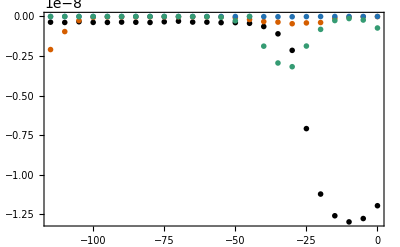

```mathematica
ListPlot[Transpose[{dat[#][[All,2]]-dat[#][[All,1]],dat[#][[All,3]]}]&/@{"fd","ct","cb","he"},PlotRange->Full]
```

```mathematica
PlotDeflectorData[datAll["fd"],1/5,"Test"]
```

-Graphics-

```mathematica
Map[PlotDeflectorData[datAll[#],1/5,#]&,{"ct","cb","he"}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
date=DateString["2021-06-16",{"Year","-","Month","-","Day"}]
timeString="141122";
fn=FileNameJoin[{"16","deflectorTransmission"<>date<>"_"<>timeString<>".dat"}]
step=-5;
stepEast=step;
stepWest=step;
east={135};
west=Range[20,0,stepWest];
pairs=Partition[Flatten[Outer[List,east,west]],2]
```

2021-06-16

16\deflectorTransmission2021-06-16_141122.dat

{{135,20},{135,15},{135,10},{135,5},{135,0}}

<|fd→{{135,20,-2.9675×10^-10},{135,15,-3.3669×10^-10},{135,10,-2.7358×10^-10},{135,5,-2.845×10^-10},{135,0,-2.8444×10^-10}},ct→{{135,20,-1.9108×10^-9},{135,15,-4.353×10^-9},{135,10,-6.602×10^-9},{135,5,-6.632×10^-9},{135,0,-6.307×10^-9}},cb→{{135,20,-2.×10^-12},{135,15,-2.×10^-12},{135,10,-2.4×10^-12},{135,5,-3.3×10^-12},{135,0,-5.6×10^-12}},he→{{135,20,-5.9×10^-12},{135,15,-1.18×10^-11},{135,10,-1.64×10^-11},{135,5,-1.74×10^-11},{135,0,-3.12×10^-11}}|>

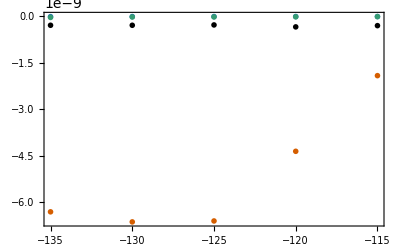

```mathematica
dat2=OrganizeDeflectorData[fn,pairs]
ListPlot[Transpose[{dat[#][[All,2]]-dat[#][[All,1]],dat[#][[All,3]]}]&/@{"fd","ct","cb","he"},PlotRange->Full]
```

<|fd→{{20,20,-1.19664×10^-8},{25,20,-1.27764×10^-8},{30,20,-1.29889×10^-8},{35,20,-1.26016×10^-8},{40,20,-1.12291×10^-8},{45,20,-7.0913×10^-9},{50,20,-2.1426×10^-9},{55,20,-1.09801×10^-9},{60,20,-6.3681×10^-10},{65,20,-4.3247×10^-10},{70,20,-3.8912×10^-10},{75,20,-3.9036×10^-10},{80,20,-3.5909×10^-10},{85,20,-3.5511×10^-10},{90,20,-2.9828×10^-10},{95,20,-3.3688×10^-10},{100,20,-3.8027×10^-10},{105,20,-3.6544×10^-10},{110,20,-3.5579×10^-10},{115,20,-3.7626×10^-10},{120,20,-3.7577×10^-10},{125,20,-3.3357×10^-10},{130,20,-3.7967×10^-10},{135,20,-3.6127×10^-10},{135,20,-2.9675×10^-10},{135,15,-3.3669×10^-10},{135,10,-2.7358×10^-10},{135,5,-2.845×10^-10},{135,0,-2.8444×10^-10}},ct→{{20,20,-7.6×10^-12},{25,20,-2.×10^-11},{30,20,-4.35×10^-11},{35,20,-1.167×10^-10},{40,20,-3.832×10^-10},{45,20,-4.079×10^-10},{50,20,-4.58×10^-10},{55,20,-3.565×10^-10},{60,20,-3.228×10^-10},{65,20,-1.92×10^-10},{70,20,-7.87×10^-11},{75,20,-3.15×10^-11},{80,20,-2.31×10^-11},{85,20,-2.26×10^-11},{90,20,-2.25×10^-11},{95,20,-2.34×10^-11},{100,20,-2.49×10^-11},{105,20,-2.55×10^-11},{110,20,-2.71×10^-11},{115,20,-3.06×10^-11},{120,20,-5.88×10^-11},{125,20,-2.524×10^-10},{130,20,-9.562×10^-10},{135,20,-2.093×10^-9},{135,20,-1.9108×10^-9},{135,15,-4.353×10^-9},{135,10,-6.602×10^-9},{135,5,-6.632×10^-9},{135,0,-6.307×10^-9}},cb→{{20,20,-2.3×10^-12},{25,20,-1.7×10^-12},{30,20,-1.4×10^-12},{35,20,-9.×10^-13},{40,20,-3.1×10^-12},{45,20,-9.4×10^-12},{50,20,-1.8×10^-11},{55,20,-1.68×10^-11},{60,20,-1.11×10^-11},{65,20,-5.×10^-12},{70,20,-2.6×10^-12},{75,20,-1.9×10^-12},{80,20,-1.8×10^-12},{85,20,-1.8×10^-12},{90,20,-1.9×10^-12},{95,20,-1.8×10^-12},{100,20,-1.8×10^-12},{105,20,-1.9×10^-12},{110,20,-1.8×10^-12},{115,20,-1.9×10^-12},{120,20,-1.8×10^-12},{125,20,-1.9×10^-12},{130,20,-1.9×10^-12},{135,20,-2.×10^-12},{135,20,-2.×10^-12},{135,15,-2.×10^-12},{135,10,-2.4×10^-12},{135,5,-3.3×10^-12},{135,0,-5.6×10^-12}},he→{{20,20,-7.293×10^-10},{25,20,-2.264×10^-10},{30,20,-1.329×10^-10},{35,20,-2.585×10^-10},{40,20,-8.158×10^-10},{45,20,-1.871×10^-9},{50,20,-3.177×10^-9},{55,20,-2.942×10^-9},{60,20,-1.878×10^-9},{65,20,0.},{70,20,-2.738×10^-10},{75,20,-5.04×10^-11},{80,20,-1.84×10^-11},{85,20,-8.3×10^-12},{90,20,-5.2×10^-12},{95,20,-3.4×10^-12},{100,20,-2.6×10^-12},{105,20,-2.5×10^-12},{110,20,-2.9×10^-12},{115,20,-3.4×10^-12},{120,20,-4.×10^-12},{125,20,-4.7×10^-12},{130,20,-5.6×10^-12},{135,20,-6.4×10^-12},{135,20,-5.9×10^-12},{135,15,-1.18×10^-11},{135,10,-1.64×10^-11},{135,5,-1.74×10^-11},{135,0,-3.12×10^-11}}|>

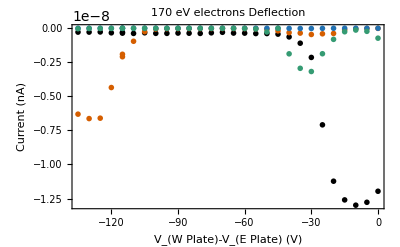

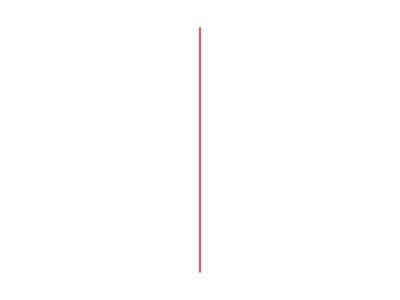

```mathematica
datAll=Merge[{dat,dat2},Catenate]
pl=ListPlot[Transpose[{datAll[#][[All,2]]-datAll[#][[All,1]],datAll[#][[All,3]]}]&/@{"fd","ct","cb","he"},PlotRange->Full,FrameLabel->{"V_(W Plate)-V_(E Plate) (V)","Current (nA)"},PlotLabel->"170 eV electrons Deflection"]
graph=Graphics[{Red,Line[{{-115,0},{-115,-2*^-8}}]}]
```

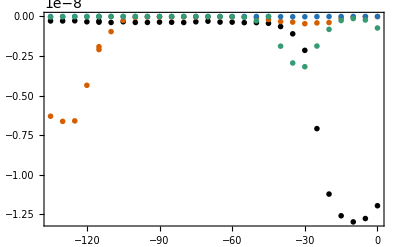

-Graphics-

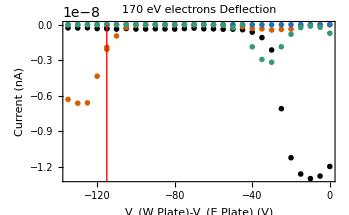

```mathematica
Show[{pl,graph}]
```

```mathematica
date="2021-06-16";
username=SystemInformation["Kernel","Username"];
(* If the username is kahrendsen2, we're on the lab computer, so we can access the raspberry pi on the network. Otherwise, use the backup on Box. *)
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
rbData=FileNameJoin[{$HomeDirectory,"OneDrive - University of Nebraska-Lincoln","Gay Group","Project - Rb Spin Filter","RbDataRaw"}];
];
(* Rb 9, pg. 140 *)
timeStamp="141808";
numRuns=2;
fileString=Flatten[FileNames[FileNameJoin[{rbData,date,"*"<>timeStamp<>"*.dat"}]]]
fileNames=FileNames[FileNameJoin[{rbData,date,"*.dat"}]];
pos=Flatten[Position[fileNames,fileString[[1]]]][[1]];
fileNames=fileNames[[pos;;pos+numRuns-1]];
day=StringTake[date,-2];
If[DirectoryQ[day],,CreateDirectory[day]];
Map[CopyFile[#,FileNameJoin[{day,FileNameTake[#]}]]&,fileNames];
newFileStrings=Map[FileNameJoin[{day,FileNameTake[#]}]&,fileNames];
```

{\\129.93.33.132\PiShare\RbData\2021-06-16\deflectorTransmission2021-06-16_141808.dat}

2021-06-16

16\deflectorTransmission2021-06-16_141808.dat

{{20,20},{25,20},{30,20},{35,20},{40,20},{45,20},{50,20},{55,20},{60,20},{65,20},{70,20},{75,20},{80,20},{85,20},{90,20},{95,20},{100,20},{105,20},{110,20},{115,20},{120,20},{125,20},{130,20},{135,20}}

<|fd→{{20,20,-1.2414×10^-8},{25,20,-1.31244×10^-8},{30,20,-1.29931×10^-8},{35,20,-1.1732×10^-8},{40,20,-6.9685×10^-9},{45,20,-2.4557×10^-9},{50,20,-1.18362×10^-9},{55,20,-5.9142×10^-10},{60,20,-3.563×10^-10},{65,20,-3.4233×10^-10},{70,20,-3.2764×10^-10},{75,20,-3.4869×10^-10},{80,20,-3.3331×10^-10},{85,20,-3.409×10^-10},{90,20,-3.2617×10^-10},{95,20,-3.4891×10^-10},{100,20,-3.3642×10^-10},{105,20,-3.477×10^-10},{110,20,-3.4022×10^-10},{115,20,-4.1437×10^-10},{120,20,-3.6345×10^-10},{125,20,-3.8224×10^-10},{130,20,-3.4455×10^-10},{135,20,-3.5716×10^-10}},ct→{{20,20,-7.2×10^-12},{25,20,-8.7×10^-12},{30,20,-1.32×10^-11},{35,20,-1.122×10^-10},{40,20,-3.702×10^-10},{45,20,-3.069×10^-10},{50,20,-3.867×10^-10},{55,20,-3.859×10^-10},{60,20,-1.635×10^-10},{65,20,-3.14×10^-11},{70,20,-1.8×10^-11},{75,20,-1.56×10^-11},{80,20,-1.63×10^-11},{85,20,-1.66×10^-11},{90,20,-1.83×10^-11},{95,20,-2.01×10^-11},{100,20,-2.77×10^-11},{105,20,-1.023×10^-10},{110,20,-5.346×10^-10},{115,20,-2.249×10^-9},{120,20,-5.538×10^-9},{125,20,-6.769×10^-9},{130,20,-6.195×10^-9},{135,20,-5.647×10^-9}},cb→{{20,20,-2.2×10^-12},{25,20,-1.8×10^-12},{30,20,-1.6×10^-12},{35,20,-7.×10^-13},{40,20,-2.5×10^-12},{45,20,-6.4×10^-12},{50,20,-7.5×10^-12},{55,20,-4.7×10^-12},{60,20,-3.1×10^-12},{65,20,-1.8×10^-12},{70,20,-1.7×10^-12},{75,20,-1.9×10^-12},{80,20,-1.9×10^-12},{85,20,-1.8×10^-12},{90,20,-1.8×10^-12},{95,20,-1.7×10^-12},{100,20,-1.8×10^-12},{105,20,-1.8×10^-12},{110,20,-2.×10^-12},{115,20,-2.×10^-12},{120,20,-2.3×10^-12},{125,20,-2.3×10^-12},{130,20,-1.9×10^-12},{135,20,-2.×10^-12}},he→{{20,20,-4.793×10^-10},{25,20,-1.491×10^-10},{30,20,-2.549×10^-10},{35,20,-1.1169×10^-9},{40,20,-3.929×10^-9},{45,20,-5.018×10^-9},{50,20,-2.517×10^-9},{55,20,-9.325×10^-10},{60,20,-1.79×10^-10},{65,20,-5.8×10^-11},{70,20,-1.04×10^-11},{75,20,-4.4×10^-12},{80,20,-1.9×10^-12},{85,20,-1.2×10^-12},{90,20,-1.2×10^-12},{95,20,-1.8×10^-12},{100,20,-3.4×10^-12},{105,20,-4.1×10^-12},{110,20,-9.8×10^-12},{115,20,-9.8×10^-12},{120,20,-1.15×10^-11},{125,20,-1.1×10^-11},{130,20,-8.8×10^-12},{135,20,-7.4×10^-12}}|>

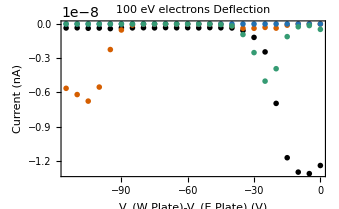

```mathematica
date=DateString["2021-06-16",{"Year","-","Month","-","Day"}]
timeString="141808";
fn=FileNameJoin[{"16","deflectorTransmission"<>date<>"_"<>timeString<>".dat"}]
step=5;
stepEast=step;
stepWest=step;
east=Range[20,135,stepWest];
west={20};
pairs=Partition[Flatten[Outer[List,east,west]],2]
dat=OrganizeDeflectorData[fn,pairs]
ListPlot[Transpose[{dat[#][[All,2]]-dat[#][[All,1]],dat[#][[All,3]]}]&/@{"fd","ct","cb","he"},PlotRange->Full,
FrameLabel->{"V_(W Plate)-V_(E Plate) (V)","Current (nA)"},PlotLabel->"100 eV electrons Deflection"]
```

2021-06-16

16\deflectorTransmission2021-06-16_142358.dat

{{20,20},{25,20},{30,20},{35,20},{40,20},{45,20},{50,20},{55,20},{60,20},{65,20},{70,20},{75,20},{80,20},{85,20},{90,20},{95,20},{100,20},{105,20},{110,20},{115,20},{120,20},{125,20},{130,20},{135,20}}

<|fd→{{20,20,-1.27595×10^-8},{25,20,-1.32282×10^-8},{30,20,-1.2749×10^-8},{35,20,-7.9713×10^-9},{40,20,-1.75414×10^-9},{45,20,-6.4392×10^-10},{50,20,-3.7192×10^-10},{55,20,-3.3822×10^-10},{60,20,-3.3326×10^-10},{65,20,-3.4423×10^-10},{70,20,-3.3662×10^-10},{75,20,-3.4348×10^-10},{80,20,-3.8877×10^-10},{85,20,-3.6543×10^-10},{90,20,-3.4761×10^-10},{95,20,-3.404×10^-10},{100,20,-2.9311×10^-10},{105,20,-2.9598×10^-10},{110,20,-3.2667×10^-10},{115,20,-3.7621×10^-10},{120,20,-3.1183×10^-10},{125,20,-3.0484×10^-10},{130,20,-3.0472×10^-10},{135,20,-2.966×10^-10}},ct→{{20,20,-6.9×10^-12},{25,20,-9.6×10^-12},{30,20,-2.76×10^-11},{35,20,-5.075×10^-10},{40,20,-8.461×10^-10},{45,20,-2.427×10^-10},{50,20,-6.42×10^-11},{55,20,-2.56×10^-11},{60,20,-9.1×10^-12},{65,20,-7.7×10^-12},{70,20,-8.×10^-12},{75,20,-9.1×10^-12},{80,20,-1.05×10^-11},{85,20,-1.44×10^-11},{90,20,-3.64×10^-11},{95,20,-1.968×10^-10},{100,20,-1.0251×10^-9},{105,20,-2.937×10^-9},{110,20,-5.552×10^-9},{115,20,-6.834×10^-9},{120,20,-6.425×10^-9},{125,20,-5.717×10^-9},{130,20,-5.299×10^-9},{135,20,-5.17×10^-9}},cb→{{20,20,-2.1×10^-12},{25,20,-1.7×10^-12},{30,20,-1.6×10^-12},{35,20,-9.×10^-13},{40,20,-4.3×10^-12},{45,20,-3.3×10^-12},{50,20,-2.3×10^-12},{55,20,-1.9×10^-12},{60,20,-1.9×10^-12},{65,20,-1.8×10^-12},{70,20,-1.8×10^-12},{75,20,-1.9×10^-12},{80,20,-1.7×10^-12},{85,20,-1.8×10^-12},{90,20,-1.8×10^-12},{95,20,-1.9×10^-12},{100,20,-1.7×10^-12},{105,20,-1.9×10^-12},{110,20,-2.1×10^-12},{115,20,-2.×10^-12},{120,20,-2.1×10^-12},{125,20,-2.×10^-12},{130,20,-2.×10^-12},{135,20,-2.×10^-12}},he→{{20,20,-3.077×10^-10},{25,20,-7.59×10^-11},{30,20,-3.613×10^-10},{35,20,-2.591×10^-9},{40,20,-4.167×10^-9},{45,20,-2.557×10^-9},{50,20,-5.596×10^-10},{55,20,-1.296×10^-10},{60,20,-1.751×10^-10},{65,20,-8.44×10^-11},{70,20,-1.56×10^-11},{75,20,-1.3×10^-12},{80,20,-5.×10^-13},{85,20,-9.×10^-13},{90,20,-1.5×10^-12},{95,20,-2.2×10^-12},{100,20,-7.9×10^-12},{105,20,-9.1×10^-12},{110,20,-1.1×10^-11},{115,20,-9.5×10^-12},{120,20,-1.15×10^-11},{125,20,-1.62×10^-11},{130,20,-2.33×10^-11},{135,20,-2.63×10^-11}}|>

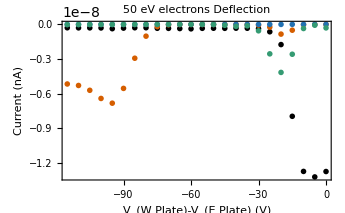

```mathematica
date=DateString["2021-06-16",{"Year","-","Month","-","Day"}]
timeString="142358";
fn=FileNameJoin[{"16","deflectorTransmission"<>date<>"_"<>timeString<>".dat"}]
step=5;
stepEast=step;
stepWest=step;
east=Range[20,135,stepWest];
west={20};
pairs=Partition[Flatten[Outer[List,east,west]],2]
dat=OrganizeDeflectorData[fn,pairs]
ListPlot[Transpose[{dat[#][[All,2]]-dat[#][[All,1]],dat[#][[All,3]]}]&/@{"fd","ct","cb","he"},PlotRange->Full,
FrameLabel->{"V_(W Plate)-V_(E Plate) (V)","Current (nA)"},PlotLabel->"50 eV electrons Deflection"]
```

## 2021-06-25

I decided that I wanted to look at time dependence with the deflector data. So I added in a loop so that 10 measurements are collected when Enter is pressed. That means I have to make some adjustments on how I process the code.  Here is the current state of affairs for a single measurement.

```mathematica
OrganizeDeflectorData[fn_(*filename*),vp_(*voltage pairs*)]:=Module[{sr=11(*startRow*),
er(*endRow*),
ri=Import[fn](* raw import*),
v (*values*), 
sig(*signal*),
graphs},
er=sr+Length[vp]-1;
v=ri[[sr;;er]]; (* (v)alues *)
sig=Transpose[v];(* There are columns for error, but currently they aren't populated. So we only take the odd columns *)
sig=<|"fd"->sig[[1]],(*fd=faraday collector*)
"ct"->sig[[3]],(* ct=chiral top *)
"cb"->sig[[5]], (* cb=chiral bottom *)
"he"->sig[[7]]|>; (* he=helium target*)
sig["he"]=sig["he"];


sig=Map[Flatten[Riffle[vp,#]]&,sig]; (* Combine signal and voltage pairs *)
sig= Map[Partition[#,3]&,sig] (* Organize the signal and voltage pairs into {east voltage, west voltage, signal} *)
];
```

I add in another argument indicating the number of measurements that are repeated at each point.

```mathematica
OrganizeDeflectorDataWithTime[fn_(*filename*),vp_(*voltage pairs*),measurementsAtPoint_:1,type_String:"Mean"]:=Module[{sr=11(*startRow*),
er(*endRow*),
ri=Import[fn](* raw import*),
v (*values*), 
sig(*signal*),
graphs,
SevenSecondSlope},
SevenSecondSlope[list_List]:=Abs[list[[-1]]]-Abs[list[[1]]];
er=sr+Length[vp]*measurementsAtPoint-1;
v=ri[[sr;;er]]; (* (v)alues *)
sig=Transpose[v];(* There are columns for error, but currently they aren't populated. So we only take the odd columns *)
sig=<|"fd"->sig[[1]],(*fd=faraday collector*)
"ct"->sig[[3]],(* ct=chiral top *)
"cb"->sig[[5]], (* cb=chiral bottom *)
"he"->sig[[7]]|>; (* he=helium target*)
sig["he"]=sig["he"];
sig=Map[Partition[#,measurementsAtPoint]&,sig];
Switch[type,
"Mean",sig=Map[Mean,sig,{2}];,
"Slope",sig=Map[SevenSecondSlope,sig,{2}];
];

sig=Map[Flatten[Riffle[vp,#]]&,sig]; (* Combine signal and voltage pairs *)
sig= Map[Partition[#,3]&,sig] (* Organize the signal and voltage pairs into {east voltage, west voltage, signal} *)
]
```

I’ll need to repeat the voltage pairs. I’m not really sure how to do this... Something with a constant array maybe...

```mathematica
vp={{0,0},{0,5},{0,10}};
Map[ConstantArray[#,10]&,vp]
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5}},{{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10}}}

That’s the ticket! Add in a flatten and we’re good to go- But are we really? We don’t want to just pair up the current readings with the correct voltage pairs, we want to extract the behavior of the repeated measurements.

```mathematica
vp={{0,0},{0,5},{0,10}};
flat=Flatten[Map[ConstantArray[#,10]&,vp]]
Partition[flat,2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,5,0,5,0,5,0,5,0,5,0,5,0,5,0,5,0,5,0,10,0,10,0,10,0,10,0,10,0,10,0,10,0,10,0,10,0,10}

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,5},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10},{0,10}}

```mathematica
fileString=FileNameJoin[{$DATARUNS,"2021","06","24","*172842.dat"}];
ri=Import[FileNames[fileString][[1]]];
sr=11;
measurementsAtPoint=10;
```

Making the combinations of voltages used should be second nature at this point, but I copy and paste too much.

```mathematica
east=Range[50,80,10];
west=Range[-50,-80,-10];
vp=Partition[Flatten[Outer[List,east,west]],2]
```

{{50,-50},{50,-60},{50,-70},{50,-80},{60,-50},{60,-60},{60,-70},{60,-80},{70,-50},{70,-60},{70,-70},{70,-80},{80,-50},{80,-60},{80,-70},{80,-80}}

```mathematica
er=sr+Length[vp]*measurementsAtPoint-1;
v=ri[[sr;;er]]; (* (v)alues *)
sig=Transpose[v];(* There are columns for error, but currently they aren't populated. So we only take the odd columns *)
sig=<|"fd"->sig[[1]],(*fd=faraday collector*)
"ct"->sig[[3]],(* ct=chiral top *)
"cb"->sig[[5]], (* cb=chiral bottom *)
"he"->sig[[7]]|>; (* he=helium target*)
sig["he"]=sig["he"];
(*
sig=Map[Flatten[Riffle[vp,#]]&,sig]; (* Combine signal and voltage pairs *)
sig= Map[Partition[#,3]&,sig] (* Organize the signal and voltage pairs into {east voltage, west voltage, signal} *)
*)
```

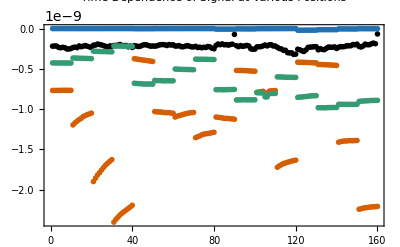

```mathematica
ListPlot[sig,PlotRange->Full,PlotLabel->"Time Dependence of Signal\nat Various Positions"]
```

```mathematica
partitionedMeasurements=Map[Partition[#,10]&,sig]
```

<|fd→{{-2.184×10^-10,-2.1615×10^-10,-2.1729×10^-10,-2.3463×10^-10,-2.3814×10^-10,-2.3254×10^-10,-2.3688×10^-10,-2.5333×10^-10,-2.5352×10^-10,-2.4754×10^-10},{-2.3487×10^-10,-2.3016×10^-10,-2.3666×10^-10,-2.1498×10^-10,-2.2487×10^-10,-2.185×10^-10,-2.1103×10^-10,-2.1952×10^-10,-2.2706×10^-10,-2.3418×10^-10},{-2.0586×10^-10,-2.0463×10^-10,-1.9179×10^-10,-1.9816×10^-10,-2.032×10^-10,-2.1226×10^-10,-2.2055×10^-10,-2.3254×10^-10,-2.1561×10^-10,-2.1831×10^-10},{-2.0958×10^-10,-2.1027×10^-10,-2.0521×10^-10,-1.9805×10^-10,-2.0993×10^-10,-2.1025×10^-10,-2.1014×10^-10,-2.2625×10^-10,-2.1657×10^-10,-2.3436×10^-10},{-2.1237×10^-10,-2.1635×10^-10,-2.2264×10^-10,-2.1852×10^-10,-2.0635×10^-10,-2.0024×10^-10,-2.0208×10^-10,-2.1143×10^-10,-2.1851×10^-10,-2.1607×10^-10},{-2.1823×10^-10,-2.144×10^-10,-2.0511×10^-10,-1.9966×10^-10,-1.9834×10^-10,-2.012×10^-10,-2.099×10^-10,-1.9827×10^-10,-2.0405×10^-10,-2.0125×10^-10},{-2.1668×10^-10,-2.1595×10^-10,-2.1207×10^-10,-2.2487×10^-10,-2.2578×10^-10,-2.1779×10^-10,-2.1123×10^-10,-2.1929×10^-10,-2.2695×10^-10,-2.2776×10^-10},{-2.1968×10^-10,-2.3498×10^-10,-2.3054×10^-10,-2.3844×10^-10,-2.3205×10^-10,-2.345×10^-10,-2.2237×10^-10,-2.2746×10^-10,-2.4316×10^-10,-2.5085×10^-10},{-2.0876×10^-10,-1.9163×10^-10,-2.0012×10^-10,-1.9005×10^-10,-2.0123×10^-10,-1.9872×10^-10,-2.0551×10^-10,-1.9817×10^-10,-1.9368×10^-10,-7.2208×10^-11},{-2.125×10^-10,-2.2449×10^-10,-2.1111×10^-10,-2.2005×10^-10,-2.1617×10^-10,-2.0905×10^-10,-2.1574×10^-10,-2.5019×10^-10,-2.5639×10^-10,-2.5477×10^-10},{-2.2698×10^-10,-2.2577×10^-10,-2.2352×10^-10,-2.1504×10^-10,-2.0363×10^-10,-2.1506×10^-10,-2.0258×10^-10,-2.0126×10^-10,-2.1522×10^-10,-2.1726×10^-10},{-2.321×10^-10,-2.4788×10^-10,-2.5322×10^-10,-2.6985×10^-10,-2.6956×10^-10,-2.9887×10^-10,-3.0207×10^-10,-3.0097×10^-10,-3.2025×10^-10,-3.1739×10^-10},{-2.5555×10^-10,-2.6285×10^-10,-2.7549×10^-10,-2.8413×10^-10,-2.6497×10^-10,-2.3414×10^-10,-2.2993×10^-10,-2.2906×10^-10,-2.2491×10^-10,-2.246×10^-10},{-2.6351×10^-10,-2.4976×10^-10,-2.5916×10^-10,-2.6149×10^-10,-2.4608×10^-10,-2.2917×10^-10,-2.3151×10^-10,-2.3272×10^-10,-2.2727×10^-10,-2.4728×10^-10},{-2.3136×10^-10,-2.2316×10^-10,-2.2607×10^-10,-2.2251×10^-10,-2.1366×10^-10,-2.1412×10^-10,-2.1241×10^-10,-1.9771×10^-10,-2.0086×10^-10,-1.9321×10^-10},{-2.2164×10^-10,-2.2902×10^-10,-2.1593×10^-10,-1.9272×10^-10,-2.0036×10^-10,-2.0036×10^-10,-1.8936×10^-10,-1.7999×10^-10,-1.8791×10^-10,-6.6785×10^-11}},ct→{{-7.673×10^-10,-7.676×10^-10,-7.673×10^-10,-7.676×10^-10,-7.66×10^-10,-7.668×10^-10,-7.66×10^-10,-7.661×10^-10,-7.665×10^-10,-7.665×10^-10},{-1.1956×10^-9,-1.1696×10^-9,-1.1488×10^-9,-1.1296×10^-9,-1.114×10^-9,-1.0909×10^-9,-1.0801×10^-9,-1.0671×10^-9,-1.0593×10^-9,-1.0488×10^-9},{-1.8987×10^-9,-1.8559×10^-9,-1.8173×10^-9,-1.7878×10^-9,-1.7532×10^-9,-1.7224×10^-9,-1.6929×10^-9,-1.6691×10^-9,-1.6473×10^-9,-1.6257×10^-9},{-2.402×10^-9,-2.367×10^-9,-2.34×10^-9,-2.312×10^-9,-2.291×10^-9,-2.271×10^-9,-2.252×10^-9,-2.233×10^-9,-2.215×10^-9,-2.193×10^-9},{-3.739×10^-10,-3.775×10^-10,-3.818×10^-10,-3.848×10^-10,-3.893×10^-10,-3.931×10^-10,-3.967×10^-10,-3.997×10^-10,-4.042×10^-10,-4.082×10^-10},{-1.0297×10^-9,-1.0327×10^-9,-1.0345×10^-9,-1.035×10^-9,-1.0397×10^-9,-1.0416×10^-9,-1.0436×10^-9,-1.0433×10^-9,-1.0487×10^-9,-1.0501×10^-9},{-1.0979×10^-9,-1.0867×10^-9,-1.0794×10^-9,-1.0728×10^-9,-1.0652×10^-9,-1.057×10^-9,-1.0518×10^-9,-1.0467×10^-9,-1.0429×10^-9,-1.0407×10^-9},{-1.3533×10^-9,-1.3414×10^-9,-1.3331×10^-9,-1.3194×10^-9,-1.3101×10^-9,-1.3049×10^-9,-1.3016×10^-9,-1.2975×10^-9,-1.2917×10^-9,-1.2869×10^-9},{-1.098×10^-9,-1.1012×10^-9,-1.1037×10^-9,-1.108×10^-9,-1.1138×10^-9,-1.1145×10^-9,-1.1151×10^-9,-1.1191×10^-9,-1.1201×10^-9,-1.1259×10^-9},{-5.195×10^-10,-5.198×10^-10,-5.196×10^-10,-5.203×10^-10,-5.215×10^-10,-5.226×10^-10,-5.247×10^-10,-5.267×10^-10,-5.277×10^-10,-5.29×10^-10},{-7.911×10^-10,-7.868×10^-10,-7.84×10^-10,-7.781×10^-10,-7.989×10^-10,-8.041×10^-10,-7.777×10^-10,-7.72×10^-10,-7.707×10^-10,-7.689×10^-10},{-1.7212×10^-9,-1.7032×10^-9,-1.6891×10^-9,-1.6748×10^-9,-1.6674×10^-9,-1.6589×10^-9,-1.6516×10^-9,-1.6441×10^-9,-1.6374×10^-9,-1.6328×10^-9},{-4.173×10^-10,-4.176×10^-10,-4.186×10^-10,-4.189×10^-10,-4.202×10^-10,-4.209×10^-10,-4.222×10^-10,-4.227×10^-10,-4.249×10^-10,-4.254×10^-10},{-4.463×10^-10,-4.457×10^-10,-4.463×10^-10,-4.479×10^-10,-4.491×10^-10,-4.499×10^-10,-4.52×10^-10,-4.539×10^-10,-4.55×10^-10,-4.573×10^-10},{-1.4097×10^-9,-1.4028×10^-9,-1.3979×10^-9,-1.3947×10^-9,-1.3948×10^-9,-1.3899×10^-9,-1.3908×10^-9,-1.3915×10^-9,-1.3891×10^-9,-1.3883×10^-9},{-2.242×10^-9,-2.236×10^-9,-2.228×10^-9,-2.224×10^-9,-2.221×10^-9,-2.217×10^-9,-2.213×10^-9,-2.211×10^-9,-2.21×10^-9,-2.207×10^-9}},cb→{{-4.×10^-13,-3.×10^-13,-3.×10^-13,-2.×10^-13,-2.×10^-13,-1.×10^-13,-1.×10^-13,-2.×10^-13,-3.×10^-13,-4.×10^-13},{0.,-3.×10^-13,-2.×10^-13,-4.×10^-13,-6.×10^-13,-6.×10^-13,-5.×10^-13,-4.×10^-13,-3.×10^-13,-2.×10^-13},{-4.×10^-13,-5.×10^-13,-4.×10^-13,-4.×10^-13,-2.×10^-13,-3.×10^-13,-1.×10^-13,-2.×10^-13,0.,-1.×10^-13},{-1.×10^-13,-1.×10^-13,0.,0.,1.×10^-13,0.,-1.×10^-13,-2.×10^-13,-4.×10^-13,-3.×10^-13},{-1.4×10^-12,-1.5×10^-12,-1.7×10^-12,-1.8×10^-12,-1.8×10^-12,-1.8×10^-12,-1.8×10^-12,-1.8×10^-12,-1.7×10^-12,-1.7×10^-12},{-7.×10^-13,-8.×10^-13,-7.×10^-13,-8.×10^-13,-7.×10^-13,-6.×10^-13,-6.×10^-13,-5.×10^-13,-4.×10^-13,-4.×10^-13},{-4.×10^-13,-4.×10^-13,-2.×10^-13,-2.×10^-13,-1.×10^-13,-1.×10^-13,0.,-1.×10^-13,0.,0.},{0.,0.,0.,-2.×10^-13,-2.×10^-13,-2.×10^-13,-3.×10^-13,-6.×10^-13,-4.×10^-13,-6.×10^-13},{-6.5×10^-12,-6.6×10^-12,-6.6×10^-12,-6.7×10^-12,-6.6×10^-12,-6.7×10^-12,-6.7×10^-12,-6.8×10^-12,-7.×10^-12,-7.1×10^-12},{-3.4×10^-12,-3.4×10^-12,-3.5×10^-12,-3.6×10^-12,-3.8×10^-12,-3.8×10^-12,-3.9×10^-12,-4.×10^-12,-3.9×10^-12,-3.8×10^-12},{-1.1×10^-12,-1.1×10^-12,-1.×10^-12,-1.×10^-12,-9.×10^-13,-8.×10^-13,-9.×10^-13,-7.×10^-13,-6.×10^-13,-5.×10^-13},{-5.×10^-13,-3.×10^-13,-3.×10^-13,-2.×10^-13,-2.×10^-13,-1.×10^-13,-1.×10^-13,0.,0.,0.},{-2.01×10^-11,-2.02×10^-11,-2.×10^-11,-1.98×10^-11,-1.96×10^-11,-1.96×10^-11,-1.96×10^-11,-1.94×10^-11,-1.95×10^-11,-1.94×10^-11},{-1.38×10^-11,-1.37×10^-11,-1.36×10^-11,-1.36×10^-11,-1.36×10^-11,-1.35×10^-11,-1.35×10^-11,-1.36×10^-11,-1.37×10^-11,-1.37×10^-11},{-3.9×10^-12,-3.8×10^-12,-4.1×10^-12,-4.×10^-12,-4.2×10^-12,-4.3×10^-12,-4.3×10^-12,-4.5×10^-12,-4.5×10^-12,-4.4×10^-12},{-1.2×10^-12,-1.2×10^-12,-1.3×10^-12,-1.3×10^-12,-1.6×10^-12,-1.8×10^-12,-1.5×10^-12,-1.6×10^-12,-1.4×10^-12,-1.2×10^-12}},he→{{-4.26×10^-10,-4.265×10^-10,-4.266×10^-10,-4.266×10^-10,-4.262×10^-10,-4.273×10^-10,-4.269×10^-10,-4.269×10^-10,-4.275×10^-10,-4.275×10^-10},{-3.65×10^-10,-3.655×10^-10,-3.666×10^-10,-3.678×10^-10,-3.69×10^-10,-3.69×10^-10,-3.701×10^-10,-3.708×10^-10,-3.718×10^-10,-3.725×10^-10},{-2.804×10^-10,-2.815×10^-10,-2.83×10^-10,-2.841×10^-10,-2.849×10^-10,-2.85×10^-10,-2.858×10^-10,-2.867×10^-10,-2.874×10^-10,-2.88×10^-10},{-2.164×10^-10,-2.163×10^-10,-2.166×10^-10,-2.168×10^-10,-2.172×10^-10,-2.18×10^-10,-2.185×10^-10,-2.191×10^-10,-2.199×10^-10,-2.203×10^-10},{-6.785×10^-10,-6.81×10^-10,-6.828×10^-10,-6.842×10^-10,-6.867×10^-10,-6.877×10^-10,-6.885×10^-10,-6.884×10^-10,-6.88×10^-10,-6.888×10^-10},{-6.433×10^-10,-6.452×10^-10,-6.458×10^-10,-6.459×10^-10,-6.48×10^-10,-6.485×10^-10,-6.47×10^-10,-6.478×10^-10,-6.485×10^-10,-6.478×10^-10},{-5.022×10^-10,-5.032×10^-10,-5.05×10^-10,-5.055×10^-10,-5.067×10^-10,-5.075×10^-10,-5.079×10^-10,-5.085×10^-10,-5.091×10^-10,-5.106×10^-10},{-3.798×10^-10,-3.801×10^-10,-3.807×10^-10,-3.807×10^-10,-3.813×10^-10,-3.813×10^-10,-3.823×10^-10,-3.831×10^-10,-3.836×10^-10,-3.839×10^-10},{-7.58×10^-10,-7.58×10^-10,-7.573×10^-10,-7.59×10^-10,-7.591×10^-10,-7.583×10^-10,-7.564×10^-10,-7.568×10^-10,-7.557×10^-10,-7.554×10^-10},{-8.856×10^-10,-8.856×10^-10,-8.852×10^-10,-8.833×10^-10,-8.833×10^-10,-8.845×10^-10,-8.839×10^-10,-8.849×10^-10,-8.842×10^-10,-8.833×10^-10},{-7.951×10^-10,-7.973×10^-10,-7.981×10^-10,-7.985×10^-10,-8.477×10^-10,-8.481×10^-10,-8.102×10^-10,-8.043×10^-10,-8.05×10^-10,-8.049×10^-10},{-5.997×10^-10,-5.996×10^-10,-6.005×10^-10,-6.017×10^-10,-6.037×10^-10,-6.041×10^-10,-6.048×10^-10,-6.047×10^-10,-6.053×10^-10,-6.058×10^-10},{-8.537×10^-10,-8.501×10^-10,-8.49×10^-10,-8.457×10^-10,-8.428×10^-10,-8.398×10^-10,-8.363×10^-10,-8.344×10^-10,-8.333×10^-10,-8.324×10^-10},{-9.822×10^-10,-9.822×10^-10,-9.812×10^-10,-9.835×10^-10,-9.817×10^-10,-9.801×10^-10,-9.801×10^-10,-9.796×10^-10,-9.793×10^-10,-9.794×10^-10},{-9.398×10^-10,-9.392×10^-10,-9.397×10^-10,-9.399×10^-10,-9.409×10^-10,-9.398×10^-10,-9.409×10^-10,-9.409×10^-10,-9.404×10^-10,-9.404×10^-10},{-9.033×10^-10,-9.005×10^-10,-8.992×10^-10,-8.976×10^-10,-8.961×10^-10,-8.942×10^-10,-8.921×10^-10,-8.921×10^-10,-8.911×10^-10,-8.911×10^-10}}|>

Okay, so now we’ve got the signal grouped so that each element of the list is a list represent the consecutive measurements taken at that voltage.

```mathematica
Mean[partitionedMeasurements]
Map[Mean,partitionedMeasurements,{2}]
```

{{-3.53025×10^-10,-3.52638×10^-10,-3.52873×10^-10,-3.57258×10^-10,-3.57635×10^-10,-3.56685×10^-10,-3.5747×10^-10,-3.61633×10^-10,-3.61955×10^-10,-3.60485×10^-10},{-4.48868×10^-10,-4.4139×10^-10,-4.38065×10^-10,-4.28195×10^-10,-4.27118×10^-10,-4.1975×10^-10,-4.15433×10^-10,-4.14455×10^-10,-4.14615×10^-10,-4.1392×10^-10},{-5.9634×10^-10,-5.85633×10^-10,-5.73123×10^-10,-5.67615×10^-10,-5.60375×10^-10,-5.5499×10^-10,-5.49838×10^-10,-5.47135×10^-10,-5.37578×10^-10,-5.33028×10^-10},{-7.0702×10^-10,-6.98418×10^-10,-6.90453×10^-10,-6.81713×10^-10,-6.79508×10^-10,-6.74813×10^-10,-6.70185×10^-10,-6.69638×10^-10,-6.62968×10^-10,-6.6199×10^-10},{-3.16543×10^-10,-3.19088×10^-10,-3.22235×10^-10,-3.2233×10^-10,-3.21038×10^-10,-3.2071×10^-10,-3.2227×10^-10,-3.25333×10^-10,-3.28103×10^-10,-3.28693×10^-10},{-4.72983×10^-10,-4.73275×10^-10,-4.71528×10^-10,-4.7034×10^-10,-4.71685×10^-10,-4.72975×10^-10,-4.75275×10^-10,-4.72468×10^-10,-4.75412×10^-10,-4.74887×10^-10},{-4.54295×10^-10,-4.51563×10^-10,-4.49168×10^-10,-4.50843×10^-10,-4.49445×10^-10,-4.45597×10^-10,-4.42732×10^-10,-4.43647×10^-10,-4.44738×10^-10,-4.44765×10^-10},{-4.88195×10^-10,-4.8912×10^-10,-4.86085×10^-10,-4.84685×10^-10,-4.80913×10^-10,-4.80225×10^-10,-4.76643×10^-10,-4.77165×10^-10,-4.79715×10^-10,-4.80563×10^-10},{-5.17815×10^-10,-5.14358×10^-10,-5.1693×10^-10,-5.15938×10^-10,-5.20182×10^-10,-5.19555×10^-10,-5.20928×10^-10,-5.20218×10^-10,-5.1912×10^-10,-4.90152×10^-10},{-4.0525×10^-10,-4.08323×10^-10,-4.04853×10^-10,-4.06813×10^-10,-4.06193×10^-10,-4.04988×10^-10,-4.0706×10^-10,-4.16447×10^-10,-4.18048×10^-10,-4.17718×10^-10},{-4.5357×10^-10,-4.52743×10^-10,-4.51655×10^-10,-4.4816×10^-10,-4.62783×10^-10,-4.67015×10^-10,-4.47845×10^-10,-4.44565×10^-10,-4.4788×10^-10,-4.4789×10^-10},{-6.38375×10^-10,-6.37745×10^-10,-6.3578×10^-10,-6.36638×10^-10,-6.35215×10^-10,-6.40493×10^-10,-6.39643×10^-10,-6.37443×10^-10,-6.40738×10^-10,-6.38998×10^-10},{-3.86662×10^-10,-3.87687×10^-10,-3.90773×10^-10,-3.92133×10^-10,-3.86893×10^-10,-3.7861×10^-10,-3.77008×10^-10,-3.7639×10^-10,-3.75653×10^-10,-3.7545×10^-10},{-4.26453×10^-10,-4.2284×10^-10,-4.25065×10^-10,-4.26623×10^-10,-4.2262×10^-10,-4.18168×10^-10,-4.19278×10^-10,-4.19955×10^-10,-4.18817×10^-10,-4.2442×10^-10},{-6.4619×10^-10,-6.4224×10^-10,-6.41942×10^-10,-6.40278×10^-10,-6.3839×10^-10,-6.3703×10^-10,-6.37103×10^-10,-6.33652×10^-10,-6.33715×10^-10,-6.31578×10^-10},{-8.42035×10^-10,-8.4168×10^-10,-8.36108×10^-10,-8.28905×10^-10,-8.29765×10^-10,-8.2834×10^-10,-8.2399×10^-10,-8.21172×10^-10,-8.22603×10^-10,-7.91521×10^-10}}

<|fd→{-2.34842×10^-10,-2.25183×10^-10,-2.10291×10^-10,-2.13061×10^-10,-2.12456×10^-10,-2.05041×10^-10,-2.19837×10^-10,-2.33403×10^-10,-1.86008×10^-10,-2.27046×10^-10,-2.14632×10^-10,-2.81216×10^-10,-2.48563×10^-10,-2.44795×10^-10,-2.13507×10^-10,-1.88408×10^-10},ct→{-7.6677×10^-10,-1.11038×10^-9,-1.74703×10^-9,-2.2876×10^-9,-3.9092×10^-10,-1.03989×10^-9,-1.06411×10^-9,-1.31399×10^-9,-1.11194×10^-9,-5.2314×10^-10,-7.8323×10^-10,-1.66805×10^-9,-4.2087×10^-10,-4.5034×10^-10,-1.39495×10^-9,-2.2209×10^-9},cb→{-2.5×10^-13,-3.5×10^-13,-2.6×10^-13,-1.1×10^-13,-1.7×10^-12,-6.2×10^-13,-1.5×10^-13,-2.5×10^-13,-6.73×10^-12,-3.71×10^-12,-8.6×10^-13,-1.7×10^-13,-1.972×10^-11,-1.363×10^-11,-4.2×10^-12,-1.41×10^-12},he→{-4.268×10^-10,-3.6881×10^-10,-2.8468×10^-10,-2.1791×10^-10,-6.8546×10^-10,-6.4678×10^-10,-5.0662×10^-10,-3.8168×10^-10,-7.574×10^-10,-8.8438×10^-10,-8.1092×10^-10,-6.0299×10^-10,-8.4175×10^-10,-9.8093×10^-10,-9.4019×10^-10,-8.9573×10^-10}|>

I have to verify that using the levelspec above I was calculating the correct means.

```mathematica
temp=partitionedMeasurements["ct"]
```

{{-7.673×10^-10,-7.676×10^-10,-7.673×10^-10,-7.676×10^-10,-7.66×10^-10,-7.668×10^-10,-7.66×10^-10,-7.661×10^-10,-7.665×10^-10,-7.665×10^-10},{-1.1956×10^-9,-1.1696×10^-9,-1.1488×10^-9,-1.1296×10^-9,-1.114×10^-9,-1.0909×10^-9,-1.0801×10^-9,-1.0671×10^-9,-1.0593×10^-9,-1.0488×10^-9},{-1.8987×10^-9,-1.8559×10^-9,-1.8173×10^-9,-1.7878×10^-9,-1.7532×10^-9,-1.7224×10^-9,-1.6929×10^-9,-1.6691×10^-9,-1.6473×10^-9,-1.6257×10^-9},{-2.402×10^-9,-2.367×10^-9,-2.34×10^-9,-2.312×10^-9,-2.291×10^-9,-2.271×10^-9,-2.252×10^-9,-2.233×10^-9,-2.215×10^-9,-2.193×10^-9},{-3.739×10^-10,-3.775×10^-10,-3.818×10^-10,-3.848×10^-10,-3.893×10^-10,-3.931×10^-10,-3.967×10^-10,-3.997×10^-10,-4.042×10^-10,-4.082×10^-10},{-1.0297×10^-9,-1.0327×10^-9,-1.0345×10^-9,-1.035×10^-9,-1.0397×10^-9,-1.0416×10^-9,-1.0436×10^-9,-1.0433×10^-9,-1.0487×10^-9,-1.0501×10^-9},{-1.0979×10^-9,-1.0867×10^-9,-1.0794×10^-9,-1.0728×10^-9,-1.0652×10^-9,-1.057×10^-9,-1.0518×10^-9,-1.0467×10^-9,-1.0429×10^-9,-1.0407×10^-9},{-1.3533×10^-9,-1.3414×10^-9,-1.3331×10^-9,-1.3194×10^-9,-1.3101×10^-9,-1.3049×10^-9,-1.3016×10^-9,-1.2975×10^-9,-1.2917×10^-9,-1.2869×10^-9},{-1.098×10^-9,-1.1012×10^-9,-1.1037×10^-9,-1.108×10^-9,-1.1138×10^-9,-1.1145×10^-9,-1.1151×10^-9,-1.1191×10^-9,-1.1201×10^-9,-1.1259×10^-9},{-5.195×10^-10,-5.198×10^-10,-5.196×10^-10,-5.203×10^-10,-5.215×10^-10,-5.226×10^-10,-5.247×10^-10,-5.267×10^-10,-5.277×10^-10,-5.29×10^-10},{-7.911×10^-10,-7.868×10^-10,-7.84×10^-10,-7.781×10^-10,-7.989×10^-10,-8.041×10^-10,-7.777×10^-10,-7.72×10^-10,-7.707×10^-10,-7.689×10^-10},{-1.7212×10^-9,-1.7032×10^-9,-1.6891×10^-9,-1.6748×10^-9,-1.6674×10^-9,-1.6589×10^-9,-1.6516×10^-9,-1.6441×10^-9,-1.6374×10^-9,-1.6328×10^-9},{-4.173×10^-10,-4.176×10^-10,-4.186×10^-10,-4.189×10^-10,-4.202×10^-10,-4.209×10^-10,-4.222×10^-10,-4.227×10^-10,-4.249×10^-10,-4.254×10^-10},{-4.463×10^-10,-4.457×10^-10,-4.463×10^-10,-4.479×10^-10,-4.491×10^-10,-4.499×10^-10,-4.52×10^-10,-4.539×10^-10,-4.55×10^-10,-4.573×10^-10},{-1.4097×10^-9,-1.4028×10^-9,-1.3979×10^-9,-1.3947×10^-9,-1.3948×10^-9,-1.3899×10^-9,-1.3908×10^-9,-1.3915×10^-9,-1.3891×10^-9,-1.3883×10^-9},{-2.242×10^-9,-2.236×10^-9,-2.228×10^-9,-2.224×10^-9,-2.221×10^-9,-2.217×10^-9,-2.213×10^-9,-2.211×10^-9,-2.21×10^-9,-2.207×10^-9}}

```mathematica
Map[Mean,temp]
```

{-7.6677×10^-10,-1.11038×10^-9,-1.74703×10^-9,-2.2876×10^-9,-3.9092×10^-10,-1.03989×10^-9,-1.06411×10^-9,-1.31399×10^-9,-1.11194×10^-9,-5.2314×10^-10,-7.8323×10^-10,-1.66805×10^-9,-4.2087×10^-10,-4.5034×10^-10,-1.39495×10^-9,-2.2209×10^-9}

```mathematica
SevenSecondSlope[list_List]:=list[[-1]]-list[[1]];
```

```mathematica
slopes=Map[SevenSecondSlope,partitionedMeasurements]
```

{8.×10^-13,1.468×10^-10,2.73×10^-10,2.09×10^-10,-3.43×10^-11,-2.04×10^-11,5.72×10^-11,6.64×10^-11,-2.79×10^-11,-9.5×10^-12,2.22×10^-11,8.84×10^-11,-8.1×10^-12,-1.1×10^-11,2.14×10^-11,3.5×10^-11}

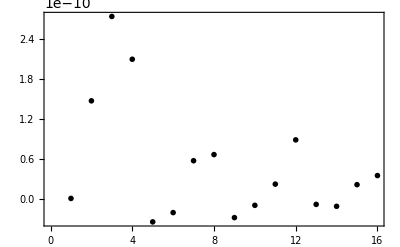

```mathematica
ListPlot[slopes]
```

```mathematica
OrganizeDeflectorData[fileString,vp,10,"Mean"]
```

Part::take: Cannot take positions 11 through 170 in {{{#Filename:,/home/pi/RbData/2021-06-24/deflectorTransmission2021-06-24_172842.dat},{#Comments:,energy=170eV,,bias=18V,,50-80,on,both,plates,E,positive,W,«8»},{#IonGauge(Torr):,3.87×10^-6},{#CVGauge(Source,Foreline)(Torr):,0.162},{#CVGauge(Target,Foreline)(Torr):,0.157},{#T_res:,38.8},{#T_res_set:,0.},{#T_trg:,48.2},{#T_trg_set:,0.},{K617,StdDev,PUMP,StdDev,PROBE,StdDev,REF,StdDev},«160»}}.

Part::partw: Part 3 of Transpose[{{{#Filename:,/home/pi/RbData/2021-06-24/deflectorTransmission2021-06-24_172842.dat},{#Comments:,energy=170eV,,bias=18V,,50-80,on,both,plates,E,positive,W,«8»},{#IonGauge(Torr):,3.87×10^-6},{#CVGauge(Source,Foreline)(Torr):,0.162},{#CVGauge(Target,Foreline)(Torr):,0.157},{#T_res:,38.8},{#T_res_set:,0.},{#T_trg:,48.2},{#T_trg_set:,0.},{K617,StdDev,PUMP,StdDev,PROBE,StdDev,REF,StdDev},«160»}}⟦11;;170⟧] does not exist.

Part::partw: Part 5 of Transpose[{{{#Filename:,/home/pi/RbData/2021-06-24/deflectorTransmission2021-06-24_172842.dat},{#Comments:,energy=170eV,,bias=18V,,50-80,on,both,plates,E,positive,W,«8»},{#IonGauge(Torr):,3.87×10^-6},{#CVGauge(Source,Foreline)(Torr):,0.162},{#CVGauge(Target,Foreline)(Torr):,0.157},{#T_res:,38.8},{#T_res_set:,0.},{#T_trg:,48.2},{#T_trg_set:,0.},{K617,StdDev,PUMP,StdDev,PROBE,StdDev,REF,StdDev},«160»}}⟦11;;170⟧] does not exist.

Part::partw: Part 7 of Transpose[{{{#Filename:,/home/pi/RbData/2021-06-24/deflectorTransmission2021-06-24_172842.dat},{#Comments:,energy=170eV,,bias=18V,,50-80,on,both,plates,E,positive,W,«8»},{#IonGauge(Torr):,3.87×10^-6},{#CVGauge(Source,Foreline)(Torr):,0.162},{#CVGauge(Target,Foreline)(Torr):,0.157},{#T_res:,38.8},{#T_res_set:,0.},{#T_trg:,48.2},{#T_trg_set:,0.},{K617,StdDev,PUMP,StdDev,PROBE,StdDev,REF,StdDev},«160»}}⟦11;;170⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

<|fd→{{50,50,Part[]},{50,60,Part[]},{50,70,Part[]},{50,80,Part[]},{60,50,Part[]},{60,60,Part[]},{60,70,Part[]},{60,80,Part[]},{70,50,Part[]},{70,60,Part[]},{70,70,Part[]},{70,80,Part[]},{80,50,Part[]},{80,60,Part[]},{80,70,Part[]}},ct→{{50,50,Part[]},{50,60,Part[]},{50,70,Part[]},{50,80,Part[]},{60,50,Part[]},{60,60,Part[]},{60,70,Part[]},{60,80,Part[]},{70,50,Part[]},{70,60,Part[]},{70,70,Part[]},{70,80,Part[]},{80,50,Part[]},{80,60,Part[]},{80,70,Part[]}},cb→{{50,50,Part[]},{50,60,Part[]},{50,70,Part[]},{50,80,Part[]},{60,50,Part[]},{60,60,Part[]},{60,70,Part[]},{60,80,Part[]},{70,50,Part[]},{70,60,Part[]},{70,70,Part[]},{70,80,Part[]},{80,50,Part[]},{80,60,Part[]},{80,70,Part[]}},he→{{50,50,Part[]},{50,60,Part[]},{50,70,Part[]},{50,80,Part[]},{60,50,Part[]},{60,60,Part[]},{60,70,Part[]},{60,80,Part[]},{70,50,Part[]},{70,60,Part[]},{70,70,Part[]},{70,80,Part[]},{80,50,Part[]},{80,60,Part[]},{80,70,Part[]}}|>

```mathematica
fn=fileString;
type="Mean"
```

Mean

```mathematica
sr=11;(*startRow*)
er;(*endRow*)
ri=Import[fn][[1]];(* raw import*)
v ;(*values*)

sig;(*signal*)
SevenSecondSlope[list_List]:=list[[-1]]-list[[1]];
er=sr+Length[vp]*measurementsAtPoint-1
v=ri[[sr;;er]]; (* (v)alues *)
sig=Transpose[v];(* There are columns for error, but currently they aren't populated. So we only take the odd columns *)
sig=<|"fd"->sig[[1]],(*fd=faraday collector*)
"ct"->sig[[3]],(* ct=chiral top *)
"cb"->sig[[5]], (* cb=chiral bottom *)
"he"->sig[[7]]|>; (* he=helium target*)
sig["he"]=sig["he"];
sig=Map[Partition[#,measurementsAtPoint]&,sig];
Switch[type,
"Mean",sig=Map[Mean,sig,{2}];,
"Slope",sig=Map[SevenSecondSlope,sig,{2}];
];

sig=Map[Flatten[Riffle[vp,#]]&,sig]; (* Combine signal and voltage pairs *)
sig= Map[Partition[#,3]&,sig] (* Organize the signal and voltage pairs into {east voltage, west voltage, signal} *)
```

170

<|fd→{{50,50,-2.34842×10^-10},{50,60,-2.25183×10^-10},{50,70,-2.10291×10^-10},{50,80,-2.13061×10^-10},{60,50,-2.12456×10^-10},{60,60,-2.05041×10^-10},{60,70,-2.19837×10^-10},{60,80,-2.33403×10^-10},{70,50,-1.86008×10^-10},{70,60,-2.27046×10^-10},{70,70,-2.14632×10^-10},{70,80,-2.81216×10^-10},{80,50,-2.48563×10^-10},{80,60,-2.44795×10^-10},{80,70,-2.13507×10^-10},{80,80,-1.88408×10^-10}},ct→{{50,50,-7.6677×10^-10},{50,60,-1.11038×10^-9},{50,70,-1.74703×10^-9},{50,80,-2.2876×10^-9},{60,50,-3.9092×10^-10},{60,60,-1.03989×10^-9},{60,70,-1.06411×10^-9},{60,80,-1.31399×10^-9},{70,50,-1.11194×10^-9},{70,60,-5.2314×10^-10},{70,70,-7.8323×10^-10},{70,80,-1.66805×10^-9},{80,50,-4.2087×10^-10},{80,60,-4.5034×10^-10},{80,70,-1.39495×10^-9},{80,80,-2.2209×10^-9}},cb→{{50,50,-2.5×10^-13},{50,60,-3.5×10^-13},{50,70,-2.6×10^-13},{50,80,-1.1×10^-13},{60,50,-1.7×10^-12},{60,60,-6.2×10^-13},{60,70,-1.5×10^-13},{60,80,-2.5×10^-13},{70,50,-6.73×10^-12},{70,60,-3.71×10^-12},{70,70,-8.6×10^-13},{70,80,-1.7×10^-13},{80,50,-1.972×10^-11},{80,60,-1.363×10^-11},{80,70,-4.2×10^-12},{80,80,-1.41×10^-12}},he→{{50,50,-4.268×10^-10},{50,60,-3.6881×10^-10},{50,70,-2.8468×10^-10},{50,80,-2.1791×10^-10},{60,50,-6.8546×10^-10},{60,60,-6.4678×10^-10},{60,70,-5.0662×10^-10},{60,80,-3.8168×10^-10},{70,50,-7.574×10^-10},{70,60,-8.8438×10^-10},{70,70,-8.1092×10^-10},{70,80,-6.0299×10^-10},{80,50,-8.4175×10^-10},{80,60,-9.8093×10^-10},{80,70,-9.4019×10^-10},{80,80,-8.9573×10^-10}}|>

```mathematica
fn
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021\06\24\*172842.dat

```mathematica
Import[fn]
```

{{{#Filename:,/home/pi/RbData/2021-06-24/deflectorTransmission2021-06-24_172842.dat},{#Comments:,energy=170eV,,bias=18V,,50-80,on,both,plates,E,positive,W,negative,,10,V,steps.,Hold,east,,step,west},{#IonGauge(Torr):,3.87×10^-6},{#CVGauge(Source,Foreline)(Torr):,0.162},{#CVGauge(Target,Foreline)(Torr):,0.157},{#T_res:,38.8},{#T_res_set:,0.},{#T_trg:,48.2},{#T_trg_set:,0.},{K617,StdDev,PUMP,StdDev,PROBE,StdDev,REF,StdDev},{-2.184×10^-10,0.,-7.673×10^-10,0.,-4.×10^-13,0.,-4.26×10^-10,0.},{-2.1615×10^-10,0.,-7.676×10^-10,0.,-3.×10^-13,0.,-4.265×10^-10,0.},{-2.1729×10^-10,0.,-7.673×10^-10,0.,-3.×10^-13,0.,-4.266×10^-10,0.},{-2.3463×10^-10,0.,-7.676×10^-10,0.,-2.×10^-13,0.,-4.266×10^-10,0.},{-2.3814×10^-10,0.,-7.66×10^-10,0.,-2.×10^-13,0.,-4.262×10^-10,0.},{-2.3254×10^-10,0.,-7.668×10^-10,0.,-1.×10^-13,0.,-4.273×10^-10,0.},{-2.3688×10^-10,0.,-7.66×10^-10,0.,-1.×10^-13,0.,-4.269×10^-10,0.},{-2.5333×10^-10,0.,-7.661×10^-10,0.,-2.×10^-13,0.,-4.269×10^-10,0.},{-2.5352×10^-10,0.,-7.665×10^-10,0.,-3.×10^-13,0.,-4.275×10^-10,0.},{-2.4754×10^-10,0.,-7.665×10^-10,0.,-4.×10^-13,0.,-4.275×10^-10,0.},{-2.3487×10^-10,0.,-1.1956×10^-9,0.,0.,0.,-3.65×10^-10,0.},{-2.3016×10^-10,0.,-1.1696×10^-9,0.,-3.×10^-13,0.,-3.655×10^-10,0.},{-2.3666×10^-10,0.,-1.1488×10^-9,0.,-2.×10^-13,0.,-3.666×10^-10,0.},{-2.1498×10^-10,0.,-1.1296×10^-9,0.,-4.×10^-13,0.,-3.678×10^-10,0.},{-2.2487×10^-10,0.,-1.114×10^-9,0.,-6.×10^-13,0.,-3.69×10^-10,0.},{-2.185×10^-10,0.,-1.0909×10^-9,0.,-6.×10^-13,0.,-3.69×10^-10,0.},{-2.1103×10^-10,0.,-1.0801×10^-9,0.,-5.×10^-13,0.,-3.701×10^-10,0.},{-2.1952×10^-10,0.,-1.0671×10^-9,0.,-4.×10^-13,0.,-3.708×10^-10,0.},{-2.2706×10^-10,0.,-1.0593×10^-9,0.,-3.×10^-13,0.,-3.718×10^-10,0.},{-2.3418×10^-10,0.,-1.0488×10^-9,0.,-2.×10^-13,0.,-3.725×10^-10,0.},{-2.0586×10^-10,0.,-1.8987×10^-9,0.,-4.×10^-13,0.,-2.804×10^-10,0.},{-2.0463×10^-10,0.,-1.8559×10^-9,0.,-5.×10^-13,0.,-2.815×10^-10,0.},{-1.9179×10^-10,0.,-1.8173×10^-9,0.,-4.×10^-13,0.,-2.83×10^-10,0.},{-1.9816×10^-10,0.,-1.7878×10^-9,0.,-4.×10^-13,0.,-2.841×10^-10,0.},{-2.032×10^-10,0.,-1.7532×10^-9,0.,-2.×10^-13,0.,-2.849×10^-10,0.},{-2.1226×10^-10,0.,-1.7224×10^-9,0.,-3.×10^-13,0.,-2.85×10^-10,0.},{-2.2055×10^-10,0.,-1.6929×10^-9,0.,-1.×10^-13,0.,-2.858×10^-10,0.},{-2.3254×10^-10,0.,-1.6691×10^-9,0.,-2.×10^-13,0.,-2.867×10^-10,0.},{-2.1561×10^-10,0.,-1.6473×10^-9,0.,0.,0.,-2.874×10^-10,0.},{-2.1831×10^-10,0.,-1.6257×10^-9,0.,-1.×10^-13,0.,-2.88×10^-10,0.},{-2.0958×10^-10,0.,-2.402×10^-9,0.,-1.×10^-13,0.,-2.164×10^-10,0.},{-2.1027×10^-10,0.,-2.367×10^-9,0.,-1.×10^-13,0.,-2.163×10^-10,0.},{-2.0521×10^-10,0.,-2.34×10^-9,0.,0.,0.,-2.166×10^-10,0.},{-1.9805×10^-10,0.,-2.312×10^-9,0.,0.,0.,-2.168×10^-10,0.},{-2.0993×10^-10,0.,-2.291×10^-9,0.,1.×10^-13,0.,-2.172×10^-10,0.},{-2.1025×10^-10,0.,-2.271×10^-9,0.,0.,0.,-2.18×10^-10,0.},{-2.1014×10^-10,0.,-2.252×10^-9,0.,-1.×10^-13,0.,-2.185×10^-10,0.},{-2.2625×10^-10,0.,-2.233×10^-9,0.,-2.×10^-13,0.,-2.191×10^-10,0.},{-2.1657×10^-10,0.,-2.215×10^-9,0.,-4.×10^-13,0.,-2.199×10^-10,0.},{-2.3436×10^-10,0.,-2.193×10^-9,0.,-3.×10^-13,0.,-2.203×10^-10,0.},{-2.1237×10^-10,0.,-3.739×10^-10,0.,-1.4×10^-12,0.,-6.785×10^-10,0.},{-2.1635×10^-10,0.,-3.775×10^-10,0.,-1.5×10^-12,0.,-6.81×10^-10,0.},{-2.2264×10^-10,0.,-3.818×10^-10,0.,-1.7×10^-12,0.,-6.828×10^-10,0.},{-2.1852×10^-10,0.,-3.848×10^-10,0.,-1.8×10^-12,0.,-6.842×10^-10,0.},{-2.0635×10^-10,0.,-3.893×10^-10,0.,-1.8×10^-12,0.,-6.867×10^-10,0.},{-2.0024×10^-10,0.,-3.931×10^-10,0.,-1.8×10^-12,0.,-6.877×10^-10,0.},{-2.0208×10^-10,0.,-3.967×10^-10,0.,-1.8×10^-12,0.,-6.885×10^-10,0.},{-2.1143×10^-10,0.,-3.997×10^-10,0.,-1.8×10^-12,0.,-6.884×10^-10,0.},{-2.1851×10^-10,0.,-4.042×10^-10,0.,-1.7×10^-12,0.,-6.88×10^-10,0.},{-2.1607×10^-10,0.,-4.082×10^-10,0.,-1.7×10^-12,0.,-6.888×10^-10,0.},{-2.1823×10^-10,0.,-1.0297×10^-9,0.,-7.×10^-13,0.,-6.433×10^-10,0.},{-2.144×10^-10,0.,-1.0327×10^-9,0.,-8.×10^-13,0.,-6.452×10^-10,0.},{-2.0511×10^-10,0.,-1.0345×10^-9,0.,-7.×10^-13,0.,-6.458×10^-10,0.},{-1.9966×10^-10,0.,-1.035×10^-9,0.,-8.×10^-13,0.,-6.459×10^-10,0.},{-1.9834×10^-10,0.,-1.0397×10^-9,0.,-7.×10^-13,0.,-6.48×10^-10,0.},{-2.012×10^-10,0.,-1.0416×10^-9,0.,-6.×10^-13,0.,-6.485×10^-10,0.},{-2.099×10^-10,0.,-1.0436×10^-9,0.,-6.×10^-13,0.,-6.47×10^-10,0.},{-1.9827×10^-10,0.,-1.0433×10^-9,0.,-5.×10^-13,0.,-6.478×10^-10,0.},{-2.0405×10^-10,0.,-1.0487×10^-9,0.,-4.×10^-13,0.,-6.485×10^-10,0.},{-2.0125×10^-10,0.,-1.0501×10^-9,0.,-4.×10^-13,0.,-6.478×10^-10,0.},{-2.1668×10^-10,0.,-1.0979×10^-9,0.,-4.×10^-13,0.,-5.022×10^-10,0.},{-2.1595×10^-10,0.,-1.0867×10^-9,0.,-4.×10^-13,0.,-5.032×10^-10,0.},{-2.1207×10^-10,0.,-1.0794×10^-9,0.,-2.×10^-13,0.,-5.05×10^-10,0.},{-2.2487×10^-10,0.,-1.0728×10^-9,0.,-2.×10^-13,0.,-5.055×10^-10,0.},{-2.2578×10^-10,0.,-1.0652×10^-9,0.,-1.×10^-13,0.,-5.067×10^-10,0.},{-2.1779×10^-10,0.,-1.057×10^-9,0.,-1.×10^-13,0.,-5.075×10^-10,0.},{-2.1123×10^-10,0.,-1.0518×10^-9,0.,0.,0.,-5.079×10^-10,0.},{-2.1929×10^-10,0.,-1.0467×10^-9,0.,-1.×10^-13,0.,-5.085×10^-10,0.},{-2.2695×10^-10,0.,-1.0429×10^-9,0.,0.,0.,-5.091×10^-10,0.},{-2.2776×10^-10,0.,-1.0407×10^-9,0.,0.,0.,-5.106×10^-10,0.},{-2.1968×10^-10,0.,-1.3533×10^-9,0.,0.,0.,-3.798×10^-10,0.},{-2.3498×10^-10,0.,-1.3414×10^-9,0.,0.,0.,-3.801×10^-10,0.},{-2.3054×10^-10,0.,-1.3331×10^-9,0.,0.,0.,-3.807×10^-10,0.},{-2.3844×10^-10,0.,-1.3194×10^-9,0.,-2.×10^-13,0.,-3.807×10^-10,0.},{-2.3205×10^-10,0.,-1.3101×10^-9,0.,-2.×10^-13,0.,-3.813×10^-10,0.},{-2.345×10^-10,0.,-1.3049×10^-9,0.,-2.×10^-13,0.,-3.813×10^-10,0.},{-2.2237×10^-10,0.,-1.3016×10^-9,0.,-3.×10^-13,0.,-3.823×10^-10,0.},{-2.2746×10^-10,0.,-1.2975×10^-9,0.,-6.×10^-13,0.,-3.831×10^-10,0.},{-2.4316×10^-10,0.,-1.2917×10^-9,0.,-4.×10^-13,0.,-3.836×10^-10,0.},{-2.5085×10^-10,0.,-1.2869×10^-9,0.,-6.×10^-13,0.,-3.839×10^-10,0.},{-2.0876×10^-10,0.,-1.098×10^-9,0.,-6.5×10^-12,0.,-7.58×10^-10,0.},{-1.9163×10^-10,0.,-1.1012×10^-9,0.,-6.6×10^-12,0.,-7.58×10^-10,0.},{-2.0012×10^-10,0.,-1.1037×10^-9,0.,-6.6×10^-12,0.,-7.573×10^-10,0.},{-1.9005×10^-10,0.,-1.108×10^-9,0.,-6.7×10^-12,0.,-7.59×10^-10,0.},{-2.0123×10^-10,0.,-1.1138×10^-9,0.,-6.6×10^-12,0.,-7.591×10^-10,0.},{-1.9872×10^-10,0.,-1.1145×10^-9,0.,-6.7×10^-12,0.,-7.583×10^-10,0.},{-2.0551×10^-10,0.,-1.1151×10^-9,0.,-6.7×10^-12,0.,-7.564×10^-10,0.},{-1.9817×10^-10,0.,-1.1191×10^-9,0.,-6.8×10^-12,0.,-7.568×10^-10,0.},{-1.9368×10^-10,0.,-1.1201×10^-9,0.,-7.×10^-12,0.,-7.557×10^-10,0.},{-7.2208×10^-11,0.,-1.1259×10^-9,0.,-7.1×10^-12,0.,-7.554×10^-10,0.},{-2.125×10^-10,0.,-5.195×10^-10,0.,-3.4×10^-12,0.,-8.856×10^-10,0.},{-2.2449×10^-10,0.,-5.198×10^-10,0.,-3.4×10^-12,0.,-8.856×10^-10,0.},{-2.1111×10^-10,0.,-5.196×10^-10,0.,-3.5×10^-12,0.,-8.852×10^-10,0.},{-2.2005×10^-10,0.,-5.203×10^-10,0.,-3.6×10^-12,0.,-8.833×10^-10,0.},{-2.1617×10^-10,0.,-5.215×10^-10,0.,-3.8×10^-12,0.,-8.833×10^-10,0.},{-2.0905×10^-10,0.,-5.226×10^-10,0.,-3.8×10^-12,0.,-8.845×10^-10,0.},{-2.1574×10^-10,0.,-5.247×10^-10,0.,-3.9×10^-12,0.,-8.839×10^-10,0.},{-2.5019×10^-10,0.,-5.267×10^-10,0.,-4.×10^-12,0.,-8.849×10^-10,0.},{-2.5639×10^-10,0.,-5.277×10^-10,0.,-3.9×10^-12,0.,-8.842×10^-10,0.},{-2.5477×10^-10,0.,-5.29×10^-10,0.,-3.8×10^-12,0.,-8.833×10^-10,0.},{-2.2698×10^-10,0.,-7.911×10^-10,0.,-1.1×10^-12,0.,-7.951×10^-10,0.},{-2.2577×10^-10,0.,-7.868×10^-10,0.,-1.1×10^-12,0.,-7.973×10^-10,0.},{-2.2352×10^-10,0.,-7.84×10^-10,0.,-1.×10^-12,0.,-7.981×10^-10,0.},{-2.1504×10^-10,0.,-7.781×10^-10,0.,-1.×10^-12,0.,-7.985×10^-10,0.},{-2.0363×10^-10,0.,-7.989×10^-10,0.,-9.×10^-13,0.,-8.477×10^-10,0.},{-2.1506×10^-10,0.,-8.041×10^-10,0.,-8.×10^-13,0.,-8.481×10^-10,0.},{-2.0258×10^-10,0.,-7.777×10^-10,0.,-9.×10^-13,0.,-8.102×10^-10,0.},{-2.0126×10^-10,0.,-7.72×10^-10,0.,-7.×10^-13,0.,-8.043×10^-10,0.},{-2.1522×10^-10,0.,-7.707×10^-10,0.,-6.×10^-13,0.,-8.05×10^-10,0.},{-2.1726×10^-10,0.,-7.689×10^-10,0.,-5.×10^-13,0.,-8.049×10^-10,0.},{-2.321×10^-10,0.,-1.7212×10^-9,0.,-5.×10^-13,0.,-5.997×10^-10,0.},{-2.4788×10^-10,0.,-1.7032×10^-9,0.,-3.×10^-13,0.,-5.996×10^-10,0.},{-2.5322×10^-10,0.,-1.6891×10^-9,0.,-3.×10^-13,0.,-6.005×10^-10,0.},{-2.6985×10^-10,0.,-1.6748×10^-9,0.,-2.×10^-13,0.,-6.017×10^-10,0.},{-2.6956×10^-10,0.,-1.6674×10^-9,0.,-2.×10^-13,0.,-6.037×10^-10,0.},{-2.9887×10^-10,0.,-1.6589×10^-9,0.,-1.×10^-13,0.,-6.041×10^-10,0.},{-3.0207×10^-10,0.,-1.6516×10^-9,0.,-1.×10^-13,0.,-6.048×10^-10,0.},{-3.0097×10^-10,0.,-1.6441×10^-9,0.,0.,0.,-6.047×10^-10,0.},{-3.2025×10^-10,0.,-1.6374×10^-9,0.,0.,0.,-6.053×10^-10,0.},{-3.1739×10^-10,0.,-1.6328×10^-9,0.,0.,0.,-6.058×10^-10,0.},{-2.5555×10^-10,0.,-4.173×10^-10,0.,-2.01×10^-11,0.,-8.537×10^-10,0.},{-2.6285×10^-10,0.,-4.176×10^-10,0.,-2.02×10^-11,0.,-8.501×10^-10,0.},{-2.7549×10^-10,0.,-4.186×10^-10,0.,-2.×10^-11,0.,-8.49×10^-10,0.},{-2.8413×10^-10,0.,-4.189×10^-10,0.,-1.98×10^-11,0.,-8.457×10^-10,0.},{-2.6497×10^-10,0.,-4.202×10^-10,0.,-1.96×10^-11,0.,-8.428×10^-10,0.},{-2.3414×10^-10,0.,-4.209×10^-10,0.,-1.96×10^-11,0.,-8.398×10^-10,0.},{-2.2993×10^-10,0.,-4.222×10^-10,0.,-1.96×10^-11,0.,-8.363×10^-10,0.},{-2.2906×10^-10,0.,-4.227×10^-10,0.,-1.94×10^-11,0.,-8.344×10^-10,0.},{-2.2491×10^-10,0.,-4.249×10^-10,0.,-1.95×10^-11,0.,-8.333×10^-10,0.},{-2.246×10^-10,0.,-4.254×10^-10,0.,-1.94×10^-11,0.,-8.324×10^-10,0.},{-2.6351×10^-10,0.,-4.463×10^-10,0.,-1.38×10^-11,0.,-9.822×10^-10,0.},{-2.4976×10^-10,0.,-4.457×10^-10,0.,-1.37×10^-11,0.,-9.822×10^-10,0.},{-2.5916×10^-10,0.,-4.463×10^-10,0.,-1.36×10^-11,0.,-9.812×10^-10,0.},{-2.6149×10^-10,0.,-4.479×10^-10,0.,-1.36×10^-11,0.,-9.835×10^-10,0.},{-2.4608×10^-10,0.,-4.491×10^-10,0.,-1.36×10^-11,0.,-9.817×10^-10,0.},{-2.2917×10^-10,0.,-4.499×10^-10,0.,-1.35×10^-11,0.,-9.801×10^-10,0.},{-2.3151×10^-10,0.,-4.52×10^-10,0.,-1.35×10^-11,0.,-9.801×10^-10,0.},{-2.3272×10^-10,0.,-4.539×10^-10,0.,-1.36×10^-11,0.,-9.796×10^-10,0.},{-2.2727×10^-10,0.,-4.55×10^-10,0.,-1.37×10^-11,0.,-9.793×10^-10,0.},{-2.4728×10^-10,0.,-4.573×10^-10,0.,-1.37×10^-11,0.,-9.794×10^-10,0.},{-2.3136×10^-10,0.,-1.4097×10^-9,0.,-3.9×10^-12,0.,-9.398×10^-10,0.},{-2.2316×10^-10,0.,-1.4028×10^-9,0.,-3.8×10^-12,0.,-9.392×10^-10,0.},{-2.2607×10^-10,0.,-1.3979×10^-9,0.,-4.1×10^-12,0.,-9.397×10^-10,0.},{-2.2251×10^-10,0.,-1.3947×10^-9,0.,-4.×10^-12,0.,-9.399×10^-10,0.},{-2.1366×10^-10,0.,-1.3948×10^-9,0.,-4.2×10^-12,0.,-9.409×10^-10,0.},{-2.1412×10^-10,0.,-1.3899×10^-9,0.,-4.3×10^-12,0.,-9.398×10^-10,0.},{-2.1241×10^-10,0.,-1.3908×10^-9,0.,-4.3×10^-12,0.,-9.409×10^-10,0.},{-1.9771×10^-10,0.,-1.3915×10^-9,0.,-4.5×10^-12,0.,-9.409×10^-10,0.},{-2.0086×10^-10,0.,-1.3891×10^-9,0.,-4.5×10^-12,0.,-9.404×10^-10,0.},{-1.9321×10^-10,0.,-1.3883×10^-9,0.,-4.4×10^-12,0.,-9.404×10^-10,0.},{-2.2164×10^-10,0.,-2.242×10^-9,0.,-1.2×10^-12,0.,-9.033×10^-10,0.},{-2.2902×10^-10,0.,-2.236×10^-9,0.,-1.2×10^-12,0.,-9.005×10^-10,0.},{-2.1593×10^-10,0.,-2.228×10^-9,0.,-1.3×10^-12,0.,-8.992×10^-10,0.},{-1.9272×10^-10,0.,-2.224×10^-9,0.,-1.3×10^-12,0.,-8.976×10^-10,0.},{-2.0036×10^-10,0.,-2.221×10^-9,0.,-1.6×10^-12,0.,-8.961×10^-10,0.},{-2.0036×10^-10,0.,-2.217×10^-9,0.,-1.8×10^-12,0.,-8.942×10^-10,0.},{-1.8936×10^-10,0.,-2.213×10^-9,0.,-1.5×10^-12,0.,-8.921×10^-10,0.},{-1.7999×10^-10,0.,-2.211×10^-9,0.,-1.6×10^-12,0.,-8.921×10^-10,0.},{-1.8791×10^-10,0.,-2.21×10^-9,0.,-1.4×10^-12,0.,-8.911×10^-10,0.},{-6.6785×10^-11,0.,-2.207×10^-9,0.,-1.2×10^-12,0.,-8.911×10^-10,0.}}}

So I learned that the Import function has an unnecessary list  level? What’s up with that?

I added in the fix, but I’m not convinced that it won’t break in the future. That extra list shouldn’t be there... AH! Yes it should. Because I’m using a regular expression to import the filename. I shouldn’t do that typically though. because I should expect the user to pass a file name instead of a regular expression.

```mathematica
fn=FileNames[fileString][[1]]
dat=OrganizeDeflectorDataWithTime[fn,vp,10,"Mean"]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021\06\24\deflectorTransmission2021-06-24_172842.dat

<|fd→{{50,-50,-2.34842×10^-10},{50,-60,-2.25183×10^-10},{50,-70,-2.10291×10^-10},{50,-80,-2.13061×10^-10},{60,-50,-2.12456×10^-10},{60,-60,-2.05041×10^-10},{60,-70,-2.19837×10^-10},{60,-80,-2.33403×10^-10},{70,-50,-1.86008×10^-10},{70,-60,-2.27046×10^-10},{70,-70,-2.14632×10^-10},{70,-80,-2.81216×10^-10},{80,-50,-2.48563×10^-10},{80,-60,-2.44795×10^-10},{80,-70,-2.13507×10^-10},{80,-80,-1.88408×10^-10}},ct→{{50,-50,-7.6677×10^-10},{50,-60,-1.11038×10^-9},{50,-70,-1.74703×10^-9},{50,-80,-2.2876×10^-9},{60,-50,-3.9092×10^-10},{60,-60,-1.03989×10^-9},{60,-70,-1.06411×10^-9},{60,-80,-1.31399×10^-9},{70,-50,-1.11194×10^-9},{70,-60,-5.2314×10^-10},{70,-70,-7.8323×10^-10},{70,-80,-1.66805×10^-9},{80,-50,-4.2087×10^-10},{80,-60,-4.5034×10^-10},{80,-70,-1.39495×10^-9},{80,-80,-2.2209×10^-9}},cb→{{50,-50,-2.5×10^-13},{50,-60,-3.5×10^-13},{50,-70,-2.6×10^-13},{50,-80,-1.1×10^-13},{60,-50,-1.7×10^-12},{60,-60,-6.2×10^-13},{60,-70,-1.5×10^-13},{60,-80,-2.5×10^-13},{70,-50,-6.73×10^-12},{70,-60,-3.71×10^-12},{70,-70,-8.6×10^-13},{70,-80,-1.7×10^-13},{80,-50,-1.972×10^-11},{80,-60,-1.363×10^-11},{80,-70,-4.2×10^-12},{80,-80,-1.41×10^-12}},he→{{50,-50,-4.268×10^-10},{50,-60,-3.6881×10^-10},{50,-70,-2.8468×10^-10},{50,-80,-2.1791×10^-10},{60,-50,-6.8546×10^-10},{60,-60,-6.4678×10^-10},{60,-70,-5.0662×10^-10},{60,-80,-3.8168×10^-10},{70,-50,-7.574×10^-10},{70,-60,-8.8438×10^-10},{70,-70,-8.1092×10^-10},{70,-80,-6.0299×10^-10},{80,-50,-8.4175×10^-10},{80,-60,-9.8093×10^-10},{80,-70,-9.4019×10^-10},{80,-80,-8.9573×10^-10}}|>

```mathematica
PlotDeflectorData[dat[[2]],1/10,"Test"]
```

-Graphics-

PlotDeflectorData

```mathematica
dat[[2]]
```

{{50,50,8.×10^-13},{50,60,1.468×10^-10},{50,70,2.73×10^-10},{50,80,2.09×10^-10},{60,50,-3.43×10^-11},{60,60,-2.04×10^-11},{60,70,5.72×10^-11},{60,80,6.64×10^-11},{70,50,-2.79×10^-11},{70,60,-9.5×10^-12},{70,70,2.22×10^-11},{70,80,8.84×10^-11},{80,50,-8.1×10^-12},{80,60,-1.1×10^-11},{80,70,2.14×10^-11},{80,80,3.5×10^-11}}

```mathematica
fn=FileNames[fileString][[1]]
dat=OrganizeDeflectorDataWithTime[fn,vp,10,"Slope"]
PlotDeflectorDataPosNeg[dat[[2]],1/10,"Test"]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021\06\24\deflectorTransmission2021-06-24_172842.dat

<|fd→{{50,-50,2.914×10^-11},{50,-60,-6.9×10^-13},{50,-70,1.245×10^-11},{50,-80,2.478×10^-11},{60,-50,3.7×10^-12},{60,-60,-1.698×10^-11},{60,-70,1.108×10^-11},{60,-80,3.117×10^-11},{70,-50,-1.36552×10^-10},{70,-60,4.227×10^-11},{70,-70,-9.72×10^-12},{70,-80,8.529×10^-11},{80,-50,-3.095×10^-11},{80,-60,-1.623×10^-11},{80,-70,-3.815×10^-11},{80,-80,-1.54855×10^-10}},ct→{{50,-50,-8.×10^-13},{50,-60,-1.468×10^-10},{50,-70,-2.73×10^-10},{50,-80,-2.09×10^-10},{60,-50,3.43×10^-11},{60,-60,2.04×10^-11},{60,-70,-5.72×10^-11},{60,-80,-6.64×10^-11},{70,-50,2.79×10^-11},{70,-60,9.5×10^-12},{70,-70,-2.22×10^-11},{70,-80,-8.84×10^-11},{80,-50,8.1×10^-12},{80,-60,1.1×10^-11},{80,-70,-2.14×10^-11},{80,-80,-3.5×10^-11}},cb→{{50,-50,0.},{50,-60,2.×10^-13},{50,-70,-3.×10^-13},{50,-80,2.×10^-13},{60,-50,3.×10^-13},{60,-60,-3.×10^-13},{60,-70,-4.×10^-13},{60,-80,6.×10^-13},{70,-50,6.×10^-13},{70,-60,4.×10^-13},{70,-70,-6.×10^-13},{70,-80,-5.×10^-13},{80,-50,-7.×10^-13},{80,-60,-1.×10^-13},{80,-70,5.×10^-13},{80,-80,0.}},he→{{50,-50,1.5×10^-12},{50,-60,7.5×10^-12},{50,-70,7.6×10^-12},{50,-80,3.9×10^-12},{60,-50,1.03×10^-11},{60,-60,4.5×10^-12},{60,-70,8.4×10^-12},{60,-80,4.1×10^-12},{70,-50,-2.6×10^-12},{70,-60,-2.3×10^-12},{70,-70,9.8×10^-12},{70,-80,6.1×10^-12},{80,-50,-2.13×10^-11},{80,-60,-2.8×10^-12},{80,-70,6.×10^-13},{80,-80,-1.22×10^-11}}|>

{-2.73×10^-10,3.43×10^-11}

-Graphics-